Kerr-Schild metric

```mathematica
$Assumptions={M>0&&-M<a<M&&-M<Q<M&&r>0&&0<θ<Pi}
```

{M>0&&-M<a<M&&-M<Q<M&&r>0&&0<θ<π}

```mathematica
HalfSimplify[expr_]:=Simplify[expr,Trig->False]
```

```mathematica
ρ=Sqrt[r^2+a^2Cos[θ]^2]
```

√(r^2+a^2 Cos[θ]^2)

```mathematica
α=1/Sqrt[1+(2M r-Q^2)/ρ^2]
```

1/(√(1+(-Q^2+2 M r)/(r^2+a^2 Cos[θ]^2)))

```mathematica
βr=α^2(2M r-Q^2)/ρ^2
```

(-Q^2+2 M r)/((r^2+a^2 Cos[θ]^2) (1+(-Q^2+2 M r)/(r^2+a^2 Cos[θ]^2)))

```mathematica
γrr=1+(2M r-Q^2)/ρ^2
```

1+(-Q^2+2 M r)/(r^2+a^2 Cos[θ]^2)

```mathematica
γrϕ=-(1+(2M r-Q^2)/ρ^2)a Sin[θ]^2
```

a (-1-(-Q^2+2 M r)/(r^2+a^2 Cos[θ]^2)) Sin[θ]^2

```mathematica
γθθ=ρ^2
```

r^2+a^2 Cos[θ]^2

```mathematica
γϕϕ=(r^2+a^2+(2M r-Q^2)/ρ^2a^2Sin[θ]^2)Sin[θ]^2
```

Sin[θ]^2 (a^2+r^2+(a^2 (-Q^2+2 M r) Sin[θ]^2)/(r^2+a^2 Cos[θ]^2))

```mathematica
(β={βr,0,0})//MatrixForm
```

((-Q^2+2 M r)/((r^2+a^2 Cos[θ]^2) (1+(-Q^2+2 M r)/(r^2+a^2 Cos[θ]^2)))
0
0)

```mathematica
(gij={{γrr,0,γrϕ},{0,γθθ,0},{γrϕ,0,γϕϕ}})//MatrixForm
```

(1+(-Q^2+2 M r)/(r^2+a^2 Cos[θ]^2) | 0 | a (-1-(-Q^2+2 M r)/(r^2+a^2 Cos[θ]^2)) Sin[θ]^2
0 | r^2+a^2 Cos[θ]^2 | 0
a (-1-(-Q^2+2 M r)/(r^2+a^2 Cos[θ]^2)) Sin[θ]^2 | 0 | Sin[θ]^2 (a^2+r^2+(a^2 (-Q^2+2 M r) Sin[θ]^2)/(r^2+a^2 Cos[θ]^2)))

```mathematica
(g0i=gij.β)//MatrixForm
```

((-Q^2+2 M r)/(r^2+a^2 Cos[θ]^2)
0
(a (-Q^2+2 M r) (-1-(-Q^2+2 M r)/(r^2+a^2 Cos[θ]^2)) Sin[θ]^2)/((r^2+a^2 Cos[θ]^2) (1+(-Q^2+2 M r)/(r^2+a^2 Cos[θ]^2))))

```mathematica
g00=-α^2+β.gij.β
```

-1/(1+(-Q^2+2 M r)/(r^2+a^2 Cos[θ]^2))+((-Q^2+2 M r)^2)/((r^2+a^2 Cos[θ]^2)^2 (1+(-Q^2+2 M r)/(r^2+a^2 Cos[θ]^2)))

```mathematica
(g={
{g00,g0i[[1]],g0i[[2]],g0i[[3]]},
{g0i[[1]],gij[[1,1]],gij[[1,2]],gij[[1,3]]},
{g0i[[2]],gij[[2,1]],gij[[2,2]],gij[[2,3]]},
{g0i[[3]],gij[[3,1]],gij[[3,2]],gij[[3,3]]}})//MatrixForm
```

(-1/(1+(-Q^2+2 M r)/(r^2+a^2 Cos[θ]^2))+((-Q^2+2 M r)^2)/((r^2+a^2 Cos[θ]^2)^2 (1+(-Q^2+2 M r)/(r^2+a^2 Cos[θ]^2))) | (-Q^2+2 M r)/(r^2+a^2 Cos[θ]^2) | 0 | (a (-Q^2+2 M r) (-1-(-Q^2+2 M r)/(r^2+a^2 Cos[θ]^2)) Sin[θ]^2)/((r^2+a^2 Cos[θ]^2) (1+(-Q^2+2 M r)/(r^2+a^2 Cos[θ]^2)))
(-Q^2+2 M r)/(r^2+a^2 Cos[θ]^2) | 1+(-Q^2+2 M r)/(r^2+a^2 Cos[θ]^2) | 0 | a (-1-(-Q^2+2 M r)/(r^2+a^2 Cos[θ]^2)) Sin[θ]^2
0 | 0 | r^2+a^2 Cos[θ]^2 | 0
(a (-Q^2+2 M r) (-1-(-Q^2+2 M r)/(r^2+a^2 Cos[θ]^2)) Sin[θ]^2)/((r^2+a^2 Cos[θ]^2) (1+(-Q^2+2 M r)/(r^2+a^2 Cos[θ]^2))) | a (-1-(-Q^2+2 M r)/(r^2+a^2 Cos[θ]^2)) Sin[θ]^2 | 0 | Sin[θ]^2 (a^2+r^2+(a^2 (-Q^2+2 M r) Sin[θ]^2)/(r^2+a^2 Cos[θ]^2)))

```mathematica
g-Transpose[g]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
(gu=Inverse[g]//HalfSimplify)//MatrixForm
```

((Q^2-r (2 M+r)-a^2 Cos[θ]^2)/(r^2+a^2 Cos[θ]^2) | -(Q^2-2 M r)/(r^2+a^2 Cos[θ]^2) | 0 | 0
-(Q^2-2 M r)/(r^2+a^2 Cos[θ]^2) | ((a^2+r^2) (Q^2-2 M r+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2)/((r^2+a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2)) | 0 | a/(a^2+r^2-a^2 Sin[θ]^2)
0 | 0 | 1/(r^2+a^2 Cos[θ]^2) | 0
0 | a/(a^2+r^2-a^2 Sin[θ]^2) | 0 | Csc[θ]^4/(-a^2+(a^2+r^2) Csc[θ]^2))

```mathematica
gu.g//HalfSimplify
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
rEH=M+Sqrt[M^2-a^2-Q^2]
```

M+√(-a^2+M^2-Q^2)

```mathematica
g//.{r->rEH,M->1,a->1/2,Q->0,θ->Pi/2}//HalfSimplify//MatrixForm
```

(7-4 √3 | 8-4 √3 | 0 | 2 (-2+√3)
8-4 √3 | 9-4 √3 | 0 | -9/2+2 √3
0 | 0 | 7/4+√3 | 0
2 (-2+√3) | -9/2+2 √3 | 0 | 4)

```mathematica
g[[4,4]]//CForm
```

Power(Sin(θ),2)*(Power(a,2) + Power(r,2) + 
     (Power(a,2)*(-Power(Q,2) + 2*M*r)*Power(Sin(θ),2))/
      (Power(r,2) + Power(a,2)*Power(Cos(θ),2)))

```mathematica
eϕ={0,0,0,1}
```

{0,0,0,1}

```mathematica
(eϕ=eϕ/Sqrt[eϕ.g.eϕ])//MatrixForm
```

(0
0
0
1/(√(Sin[θ]^2 (a^2+r^2+(a^2 (-Q^2+2 M r) Sin[θ]^2)/(r^2+a^2 Cos[θ]^2)))))

```mathematica
eθ={0,0,1,0}
```

{0,0,1,0}

```mathematica
eθ=eθ-(eθ.g.eϕ)eϕ
```

{0,0,1,0}

```mathematica
(eθ=eθ/Sqrt[eθ.g.eθ])//MatrixForm
```

(0
0
1/(√(r^2+a^2 Cos[θ]^2))
0)

```mathematica
n={-1,0,0,0}
```

{-1,0,0,0}

```mathematica
n=n-(n.eθ)eθ-(n.eϕ)eϕ
```

{-1,0,0,0}

```mathematica
(n=n/Sqrt[-n.Inverse[g].n]//HalfSimplify)//MatrixForm
```

(-(√(r^2+a^2 Cos[θ]^2))/(√(-Q^2+2 M r+r^2+a^2 Cos[θ]^2))
0
0
0)

```mathematica
n[[1]]//CForm
```

-(Sqrt(Power(r,2) + Power(a,2)*Power(Cos(θ),2))/
     Sqrt(-Power(Q,2) + 2*M*r + Power(r,2) + Power(a,2)*Power(Cos(θ),2)))

```mathematica
s={0,1,0,0}
```

{0,1,0,0}

```mathematica
s=s+(s.Inverse[g].n)n
```

{-(((r^2+a^2 Cos[θ]^2) (-(a^2 (-Q^2+2 M r) (-1-(-Q^2+2 M r)/(r^2+a^2 Cos[θ]^2))^2 Sin[θ]^4)/((r^2+a^2 Cos[θ]^2) (1+(-Q^2+2 M r)/(r^2+a^2 Cos[θ]^2)))+((-Q^2+2 M r) Sin[θ]^2 (a^2+r^2+(a^2 (-Q^2+2 M r) Sin[θ]^2)/(r^2+a^2 Cos[θ]^2)))/(r^2+a^2 Cos[θ]^2)))/((-Q^2+2 M r+r^2+a^2 Cos[θ]^2) ((-((-Q^2+2 M r)^2)/((r^2+a^2 Cos[θ]^2)^2)+(1+(-Q^2+2 M r)/(r^2+a^2 Cos[θ]^2)) (-1/(1+(-Q^2+2 M r)/(r^2+a^2 Cos[θ]^2))+((-Q^2+2 M r)^2)/((r^2+a^2 Cos[θ]^2)^2 (1+(-Q^2+2 M r)/(r^2+a^2 Cos[θ]^2))))) Sin[θ]^2 (a^2+r^2+(a^2 (-Q^2+2 M r) Sin[θ]^2)/(r^2+a^2 Cos[θ]^2))-a (-1-(-Q^2+2 M r)/(r^2+a^2 Cos[θ]^2)) Sin[θ]^2 ((a Sin[θ]^2)/(1+(-Q^2+2 M r)/(r^2+a^2 Cos[θ]^2))-(a Q^2 Sin[θ]^2)/((r^2+a^2 Cos[θ]^2) (1+(-Q^2+2 M r)/(r^2+a^2 Cos[θ]^2)))+(2 a M r Sin[θ]^2)/((r^2+a^2 Cos[θ]^2) (1+(-Q^2+2 M r)/(r^2+a^2 Cos[θ]^2))))))),1,0,0}

```mathematica
s=s-(s.eθ)eθ
```

{-(((r^2+a^2 Cos[θ]^2) (-(a^2 (-Q^2+2 M r) (-1-(-Q^2+2 M r)/(r^2+a^2 Cos[θ]^2))^2 Sin[θ]^4)/((r^2+a^2 Cos[θ]^2) (1+(-Q^2+2 M r)/(r^2+a^2 Cos[θ]^2)))+((-Q^2+2 M r) Sin[θ]^2 (a^2+r^2+(a^2 (-Q^2+2 M r) Sin[θ]^2)/(r^2+a^2 Cos[θ]^2)))/(r^2+a^2 Cos[θ]^2)))/((-Q^2+2 M r+r^2+a^2 Cos[θ]^2) ((-((-Q^2+2 M r)^2)/((r^2+a^2 Cos[θ]^2)^2)+(1+(-Q^2+2 M r)/(r^2+a^2 Cos[θ]^2)) (-1/(1+(-Q^2+2 M r)/(r^2+a^2 Cos[θ]^2))+((-Q^2+2 M r)^2)/((r^2+a^2 Cos[θ]^2)^2 (1+(-Q^2+2 M r)/(r^2+a^2 Cos[θ]^2))))) Sin[θ]^2 (a^2+r^2+(a^2 (-Q^2+2 M r) Sin[θ]^2)/(r^2+a^2 Cos[θ]^2))-a (-1-(-Q^2+2 M r)/(r^2+a^2 Cos[θ]^2)) Sin[θ]^2 ((a Sin[θ]^2)/(1+(-Q^2+2 M r)/(r^2+a^2 Cos[θ]^2))-(a Q^2 Sin[θ]^2)/((r^2+a^2 Cos[θ]^2) (1+(-Q^2+2 M r)/(r^2+a^2 Cos[θ]^2)))+(2 a M r Sin[θ]^2)/((r^2+a^2 Cos[θ]^2) (1+(-Q^2+2 M r)/(r^2+a^2 Cos[θ]^2))))))),1,0,0}

```mathematica
s=s-(s.eϕ)eϕ
```

{-(((r^2+a^2 Cos[θ]^2) (-(a^2 (-Q^2+2 M r) (-1-(-Q^2+2 M r)/(r^2+a^2 Cos[θ]^2))^2 Sin[θ]^4)/((r^2+a^2 Cos[θ]^2) (1+(-Q^2+2 M r)/(r^2+a^2 Cos[θ]^2)))+((-Q^2+2 M r) Sin[θ]^2 (a^2+r^2+(a^2 (-Q^2+2 M r) Sin[θ]^2)/(r^2+a^2 Cos[θ]^2)))/(r^2+a^2 Cos[θ]^2)))/((-Q^2+2 M r+r^2+a^2 Cos[θ]^2) ((-((-Q^2+2 M r)^2)/((r^2+a^2 Cos[θ]^2)^2)+(1+(-Q^2+2 M r)/(r^2+a^2 Cos[θ]^2)) (-1/(1+(-Q^2+2 M r)/(r^2+a^2 Cos[θ]^2))+((-Q^2+2 M r)^2)/((r^2+a^2 Cos[θ]^2)^2 (1+(-Q^2+2 M r)/(r^2+a^2 Cos[θ]^2))))) Sin[θ]^2 (a^2+r^2+(a^2 (-Q^2+2 M r) Sin[θ]^2)/(r^2+a^2 Cos[θ]^2))-a (-1-(-Q^2+2 M r)/(r^2+a^2 Cos[θ]^2)) Sin[θ]^2 ((a Sin[θ]^2)/(1+(-Q^2+2 M r)/(r^2+a^2 Cos[θ]^2))-(a Q^2 Sin[θ]^2)/((r^2+a^2 Cos[θ]^2) (1+(-Q^2+2 M r)/(r^2+a^2 Cos[θ]^2)))+(2 a M r Sin[θ]^2)/((r^2+a^2 Cos[θ]^2) (1+(-Q^2+2 M r)/(r^2+a^2 Cos[θ]^2))))))),1,0,0}

```mathematica
(s=s/Sqrt[s.Inverse[g].s]//HalfSimplify)//MatrixForm
```

((Q^2-2 M r)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) √((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2))))
1/(√((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2))))
0
0)

```mathematica
s[[2]]//CForm
```

1/Sqrt((-(Power(r,2)*(Power(a,2) + Power(r,2))) - 
       Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) + 
       Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
     ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
       (Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2))))

```mathematica
n.gu.n//Simplify
```

-1

```mathematica
s.gu.s//Simplify
```

1

```mathematica
n.gu.s//Simplify
```

0

```mathematica
n.eθ
```

0

```mathematica
n.eϕ
```

0

```mathematica
s.eθ
```

0

```mathematica
s.eϕ
```

0

```mathematica
eθ.g.eϕ
```

0

```mathematica
l=(n+s)/Sqrt[2]
```

{(-(√(r^2+a^2 Cos[θ]^2))/(√(-Q^2+2 M r+r^2+a^2 Cos[θ]^2))+(Q^2-2 M r)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) √((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2)))))/(√2),1/(√2 √((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2)))),0,0}

```mathematica
k=(n-s)/Sqrt[2]
```

{(-(√(r^2+a^2 Cos[θ]^2))/(√(-Q^2+2 M r+r^2+a^2 Cos[θ]^2))-(Q^2-2 M r)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) √((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2)))))/(√2),-1/(√2 √((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2)))),0,0}

```mathematica
l.gu.l//Simplify
```

0

```mathematica
k.gu.k//Simplify
```

0

```mathematica
l.gu.k//Simplify
```

-1

```mathematica
(q=g+Table[l[[x]]k[[y]]+k[[x]]l[[y]],{x,4},{y,4}]//HalfSimplify)//MatrixForm
```

((a^2 (Q^2-2 M r)^2 Sin[θ]^2)/((r^2+a^2 Cos[θ]^2) (r^2 (a^2+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2)) | -(a^2 (Q^2-2 M r) (-Q^2+r (2 M+r)+a^2 Cos[θ]^2) Sin[θ]^2)/((r^2+a^2 Cos[θ]^2) (r^2 (a^2+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2)) | 0 | (a (Q^2-2 M r) Sin[θ]^2)/(r^2+a^2 Cos[θ]^2)
-(a^2 (Q^2-2 M r) (-Q^2+r (2 M+r)+a^2 Cos[θ]^2) Sin[θ]^2)/((r^2+a^2 Cos[θ]^2) (r^2 (a^2+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2)) | (a^2 (-Q^2+r (2 M+r)+a^2 Cos[θ]^2)^2 Sin[θ]^2)/((r^2+a^2 Cos[θ]^2) (r^2 (a^2+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2)) | 0 | a (-1+(Q^2-2 M r)/(r^2+a^2 Cos[θ]^2)) Sin[θ]^2
0 | 0 | r^2+a^2 Cos[θ]^2 | 0
(a (Q^2-2 M r) Sin[θ]^2)/(r^2+a^2 Cos[θ]^2) | a (-1+(Q^2-2 M r)/(r^2+a^2 Cos[θ]^2)) Sin[θ]^2 | 0 | Sin[θ]^2 (a^2+r^2-(a^2 (Q^2-2 M r) Sin[θ]^2)/(r^2+a^2 Cos[θ]^2)))

```mathematica
q-Transpose[q]//HalfSimplify//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
coords={t,r,θ,ϕ}
```

{t,r,θ,ϕ}

```mathematica
(dl=Table[D[l[[x]],coords[[y]]],{x,4},{y,4}]//HalfSimplify)//MatrixForm
```

(0 | (((M+r) √(r^2+a^2 Cos[θ]^2))/((-Q^2+r (2 M+r)+a^2 Cos[θ]^2)^(3/2))-r/(√((r^2+a^2 Cos[θ]^2) (-Q^2+r (2 M+r)+a^2 Cos[θ]^2)))-(2 M)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) √((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2))))-(2 (M+r) (-Q^2+2 M r))/((-Q^2+r (2 M+r)+a^2 Cos[θ]^2)^2 √((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2))))+((Q^2-2 M r) (a^6 r Cos[θ]^4 Sin[θ]^2+Cos[θ]^2 (a^2 M (a^2+r^2)^2-2 (a^6 M+a^4 r (Q^2-r (M+r))) Sin[θ]^2+a^6 M Sin[θ]^4)+r ((Q^2-M r) (a^2+r^2)^2+a^2 (Q^4-4 Q^2 r (M+r)-2 a^2 (Q^2-M r)+r^2 (4 M^2+6 M r+r^2)) Sin[θ]^2+a^4 (Q^2-M r) Sin[θ]^4)))/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (-Q^2+r (2 M+r)+a^2 Cos[θ]^2)^2 √(a^2+r^2-a^2 Sin[θ]^2) ((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/(Q^2-r (2 M+r)-a^2 Cos[θ]^2))^(3/2)))/(√2) | (-(a^2 Cos[θ] √(r^2+a^2 Cos[θ]^2) Sin[θ])/((-Q^2+r (2 M+r)+a^2 Cos[θ]^2)^(3/2))+(a^2 Cos[θ] Sin[θ])/(√((r^2+a^2 Cos[θ]^2) (-Q^2+r (2 M+r)+a^2 Cos[θ]^2)))-(2 a^2 (Q^2-2 M r) Cos[θ] Sin[θ])/((-Q^2+r (2 M+r)+a^2 Cos[θ]^2)^2 √((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2))))-(a^2 (Q^2-2 M r) Cos[θ] Sin[θ] ((a^2+r^2) (Q^4-Q^2 r (4 M+r)+a^2 (Q^2-2 M r)+r^2 (4 M^2+2 M r+r^2))+2 a^2 (a^2+r^2) (-Q^2+r (2 M+r)) Cos[θ]^2+a^4 (a^2+r^2) Cos[θ]^4-2 a^2 (Q^2-2 M r) (a^2+r^2) Sin[θ]^2+a^4 (Q^2-2 M r) Sin[θ]^4))/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (-Q^2+r (2 M+r)+a^2 Cos[θ]^2)^2 √(a^2+r^2-a^2 Sin[θ]^2) ((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/(Q^2-r (2 M+r)-a^2 Cos[θ]^2))^(3/2)))/(√2) | 0
0 | (a^6 r Cos[θ]^4 Sin[θ]^2+Cos[θ]^2 (a^2 M (a^2+r^2)^2-2 (a^6 M+a^4 r (Q^2-r (M+r))) Sin[θ]^2+a^6 M Sin[θ]^4)+r ((Q^2-M r) (a^2+r^2)^2+a^2 (Q^4-4 Q^2 r (M+r)-2 a^2 (Q^2-M r)+r^2 (4 M^2+6 M r+r^2)) Sin[θ]^2+a^4 (Q^2-M r) Sin[θ]^4))/(√2 (Q^2-r (2 M+r)-a^2 Cos[θ]^2) √(-((a^2+r^2-a^2 Sin[θ]^2) (r^2 (a^2+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2))/(Q^2-r (2 M+r)-a^2 Cos[θ]^2)) (-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)) | (a^2 Cos[θ] Sin[θ] (-a^2-r^2+a^2 Sin[θ]^2) ((a^2+r^2) (Q^4-Q^2 r (4 M+r)+a^2 (Q^2-2 M r)+r^2 (4 M^2+2 M r+r^2))+2 a^2 (a^2+r^2) (-Q^2+r (2 M+r)) Cos[θ]^2+a^4 (a^2+r^2) Cos[θ]^4-2 a^2 (Q^2-2 M r) (a^2+r^2) Sin[θ]^2+a^4 (Q^2-2 M r) Sin[θ]^4))/(√2 (-Q^2+r (2 M+r)+a^2 Cos[θ]^2)^2 (((-a^2-r^2+a^2 Sin[θ]^2) (r^2 (a^2+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2))/(Q^2-r (2 M+r)-a^2 Cos[θ]^2))^(3/2)) | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
dl[[1,1]]//CForm
```

0

```mathematica
(Γ=Table[Sum[(1/2)gu[[x,w]](D[g[[w,y]],coords[[z]]]+D[g[[w,z]],coords[[y]]]-D[g[[y,z]],coords[[w]]]),{w,4}],{x,4},{y,4},{z,4}]//HalfSimplify)//MatrixForm
```

((((Q^2-2 M r) (r (Q^2-M r)+a^2 M Cos[θ]^2))/((r^2+a^2 Cos[θ]^2)^3)
((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (r (Q^2-M r)+a^2 M Cos[θ]^2))/((r^2+a^2 Cos[θ]^2)^3)
(a^2 (Q^2-2 M r) Cos[θ] Sin[θ])/((r^2+a^2 Cos[θ]^2)^2)
-(a (Q^2-2 M r) (r (Q^2-M r)+a^2 M Cos[θ]^2) Sin[θ]^2)/((r^2+a^2 Cos[θ]^2)^3)) | (((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (r (Q^2-M r)+a^2 M Cos[θ]^2))/((r^2+a^2 Cos[θ]^2)^3)
((Q^2-2 r (M+r)-2 a^2 Cos[θ]^2) (r (Q^2-M r)+a^2 M Cos[θ]^2))/((r^2+a^2 Cos[θ]^2)^3)
(a^2 (Q^2-2 M r) Cos[θ] Sin[θ])/((r^2+a^2 Cos[θ]^2)^2)
(a (-Q^2+r (2 M+r)+a^2 Cos[θ]^2) (r (Q^2-M r)+a^2 M Cos[θ]^2) Sin[θ]^2)/((r^2+a^2 Cos[θ]^2)^3)) | ((a^2 (Q^2-2 M r) Cos[θ] Sin[θ])/((r^2+a^2 Cos[θ]^2)^2)
(a^2 (Q^2-2 M r) Cos[θ] Sin[θ])/((r^2+a^2 Cos[θ]^2)^2)
(r (Q^2-2 M r))/(r^2+a^2 Cos[θ]^2)
-(a^3 (Q^2-2 M r) Cos[θ] Sin[θ]^3)/((r^2+a^2 Cos[θ]^2)^2)) | (-(a (Q^2-2 M r) (r (Q^2-M r)+a^2 M Cos[θ]^2) Sin[θ]^2)/((r^2+a^2 Cos[θ]^2)^3)
(a (-Q^2+r (2 M+r)+a^2 Cos[θ]^2) (r (Q^2-M r)+a^2 M Cos[θ]^2) Sin[θ]^2)/((r^2+a^2 Cos[θ]^2)^3)
-(a^3 (Q^2-2 M r) Cos[θ] Sin[θ]^3)/((r^2+a^2 Cos[θ]^2)^2)
((Q^2-2 M r) Sin[θ]^2 (r^5+a^4 r Cos[θ]^4+a^2 r (Q^2-M r) Sin[θ]^2+Cos[θ]^2 (2 a^2 r^3+a^4 M Sin[θ]^2)))/((r^2+a^2 Cos[θ]^2)^3))
(-((r (Q^2-M r)+a^2 M Cos[θ]^2) ((a^2+r^2) (Q^2-2 M r+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2))/((r^2+a^2 Cos[θ]^2)^3 (a^2+r^2-a^2 Sin[θ]^2))
-((r (Q^2-M r)+a^2 M Cos[θ]^2) ((Q^2-2 M r) (a^2+r^2)+a^2 (-Q^2+2 M r+r^2+a^2 Cos[θ]^2) Sin[θ]^2))/((r^2+a^2 Cos[θ]^2)^3 (a^2+r^2-a^2 Sin[θ]^2))
(a^4 (Q^2-2 M r) Cos[θ] Sin[θ] (-1+Cos[θ]^2+Sin[θ]^2))/((r^2+a^2 Cos[θ]^2)^2 (a^2+r^2-a^2 Sin[θ]^2))
(a (r (Q^2-M r)+a^2 M Cos[θ]^2) Sin[θ]^2 ((a^2+r^2) (Q^2-2 M r+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2))/((r^2+a^2 Cos[θ]^2)^3 (a^2+r^2-a^2 Sin[θ]^2))) | (-((r (Q^2-M r)+a^2 M Cos[θ]^2) ((Q^2-2 M r) (a^2+r^2)+a^2 (-Q^2+2 M r+r^2+a^2 Cos[θ]^2) Sin[θ]^2))/((r^2+a^2 Cos[θ]^2)^3 (a^2+r^2-a^2 Sin[θ]^2))
-((r (-Q^2+M r)-a^2 M Cos[θ]^2) ((a^2+r^2) (-Q^2+r (2 M+r))+a^2 (Q^2-2 r (M+r)) Sin[θ]^2+Cos[θ]^2 (a^4+a^2 r^2-2 a^4 Sin[θ]^2)))/((r^2+a^2 Cos[θ]^2)^3 (a^2+r^2-a^2 Sin[θ]^2))
-(a^2 Cos[θ] Sin[θ] (a^2 Q^2-2 a^2 M r+r^4+a^2 (-Q^2+2 r (M+r)) Cos[θ]^2+a^4 Cos[θ]^4-a^2 (Q^2-2 M r) Sin[θ]^2))/((r^2+a^2 Cos[θ]^2)^2 (a^2+r^2-a^2 Sin[θ]^2))
(a Sin[θ]^2 (a^6 r Cos[θ]^6+Cos[θ]^4 (3 a^4 r^3+a^6 M Sin[θ]^2)+a^2 Cos[θ]^2 (a^2 M (Q^2-2 M r)+r^2 (M Q^2-2 M^2 r+3 r^3)+a^2 (-M Q^2+2 M^2 r+Q^2 r) Sin[θ]^2)+r (a^2 (Q^4-3 M Q^2 r+2 M^2 r^2)+r^2 (Q^4-3 M Q^2 r+2 M^2 r^2+r^4)-a^2 (Q^4+M r^2 (2 M+r)-Q^2 r (3 M+r)) Sin[θ]^2)))/((r^2+a^2 Cos[θ]^2)^3 (a^2+r^2-a^2 Sin[θ]^2))) | ((a^4 (Q^2-2 M r) Cos[θ] Sin[θ] (-1+Cos[θ]^2+Sin[θ]^2))/((r^2+a^2 Cos[θ]^2)^2 (a^2+r^2-a^2 Sin[θ]^2))
-(a^2 Cos[θ] Sin[θ] (a^2 Q^2-2 a^2 M r+r^4+a^2 (-Q^2+2 r (M+r)) Cos[θ]^2+a^4 Cos[θ]^4-a^2 (Q^2-2 M r) Sin[θ]^2))/((r^2+a^2 Cos[θ]^2)^2 (a^2+r^2-a^2 Sin[θ]^2))
-(r ((a^2+r^2) (Q^2-2 M r+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2))/((r^2+a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2))
-(a^5 (Q^2-2 M r) Cos[θ] Sin[θ]^3 (-1+Cos[θ]^2+Sin[θ]^2))/((r^2+a^2 Cos[θ]^2)^2 (a^2+r^2-a^2 Sin[θ]^2))) | ((a (r (Q^2-M r)+a^2 M Cos[θ]^2) Sin[θ]^2 ((a^2+r^2) (Q^2-2 M r+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2))/((r^2+a^2 Cos[θ]^2)^3 (a^2+r^2-a^2 Sin[θ]^2))
(a Sin[θ]^2 (a^6 r Cos[θ]^6+Cos[θ]^4 (3 a^4 r^3+a^6 M Sin[θ]^2)+a^2 Cos[θ]^2 (a^2 M (Q^2-2 M r)+r^2 (M Q^2-2 M^2 r+3 r^3)+a^2 (-M Q^2+2 M^2 r+Q^2 r) Sin[θ]^2)+r (a^2 (Q^4-3 M Q^2 r+2 M^2 r^2)+r^2 (Q^4-3 M Q^2 r+2 M^2 r^2+r^4)-a^2 (Q^4+M r^2 (2 M+r)-Q^2 r (3 M+r)) Sin[θ]^2)))/((r^2+a^2 Cos[θ]^2)^3 (a^2+r^2-a^2 Sin[θ]^2))
-(a^5 (Q^2-2 M r) Cos[θ] Sin[θ]^3 (-1+Cos[θ]^2+Sin[θ]^2))/((r^2+a^2 Cos[θ]^2)^2 (a^2+r^2-a^2 Sin[θ]^2))
-(Sin[θ]^2 ((a^2+r^2) (Q^2-2 M r+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2) (r^5+a^4 r Cos[θ]^4+a^2 r (Q^2-M r) Sin[θ]^2+Cos[θ]^2 (2 a^2 r^3+a^4 M Sin[θ]^2)))/((r^2+a^2 Cos[θ]^2)^3 (a^2+r^2-a^2 Sin[θ]^2)))
((a^2 (Q^2-2 M r) Cos[θ] Sin[θ])/((r^2+a^2 Cos[θ]^2)^3)
(a^2 (Q^2-2 M r) Cos[θ] Sin[θ])/((r^2+a^2 Cos[θ]^2)^3)
0
-(a (Q^2-2 M r) Cos[θ] Sin[θ] (r^2+a^2 Cos[θ]^2+a^2 Sin[θ]^2))/((r^2+a^2 Cos[θ]^2)^3)) | ((a^2 (Q^2-2 M r) Cos[θ] Sin[θ])/((r^2+a^2 Cos[θ]^2)^3)
(a^2 (Q^2-2 M r) Cos[θ] Sin[θ])/((r^2+a^2 Cos[θ]^2)^3)
r/(r^2+a^2 Cos[θ]^2)
(a Cos[θ] Sin[θ] (r^2 (-Q^2+2 M r+r^2)+a^2 (-Q^2+2 r (M+r)) Cos[θ]^2+a^4 Cos[θ]^4-a^2 (Q^2-2 M r) Sin[θ]^2))/((r^2+a^2 Cos[θ]^2)^3)) | (0
r/(r^2+a^2 Cos[θ]^2)
-(a^2 Cos[θ] Sin[θ])/(r^2+a^2 Cos[θ]^2)
0) | (-(a (Q^2-2 M r) Cos[θ] Sin[θ] (r^2+a^2 Cos[θ]^2+a^2 Sin[θ]^2))/((r^2+a^2 Cos[θ]^2)^3)
(a Cos[θ] Sin[θ] (r^2 (-Q^2+2 M r+r^2)+a^2 (-Q^2+2 r (M+r)) Cos[θ]^2+a^4 Cos[θ]^4-a^2 (Q^2-2 M r) Sin[θ]^2))/((r^2+a^2 Cos[θ]^2)^3)
0
-(Cos[θ] Sin[θ] (r^4 (a^2+r^2)+a^4 (a^2+r^2) Cos[θ]^4+2 a^2 r^2 (-Q^2+2 M r) Sin[θ]^2-a^4 (Q^2-2 M r) Sin[θ]^4+2 Cos[θ]^2 (a^2 r^2 (a^2+r^2)-a^4 (Q^2-2 M r) Sin[θ]^2)))/((r^2+a^2 Cos[θ]^2)^3))
(-(a (r (Q^2-M r)+a^2 M Cos[θ]^2))/((r^2+a^2 Cos[θ]^2)^2 (a^2+r^2-a^2 Sin[θ]^2))
-(a (r (Q^2-M r)+a^2 M Cos[θ]^2) Csc[θ]^2)/((r^2+a^2 Cos[θ]^2)^2 (-a^2+(a^2+r^2) Csc[θ]^2))
(a (Q^2-2 M r) Cot[θ])/((r^2+a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2))
(a^2 (r (Q^2-M r)+a^2 M Cos[θ]^2) Sin[θ]^2)/((r^2+a^2 Cos[θ]^2)^2 (a^2+r^2-a^2 Sin[θ]^2))) | (-(a (r (Q^2-M r)+a^2 M Cos[θ]^2) Csc[θ]^2)/((r^2+a^2 Cos[θ]^2)^2 (-a^2+(a^2+r^2) Csc[θ]^2))
-(a (r (Q^2-M r)+a^2 M Cos[θ]^2) Csc[θ]^2)/((r^2+a^2 Cos[θ]^2)^2 (-a^2+(a^2+r^2) Csc[θ]^2))
-(a (-Q^2+r (2 M+r)+a^2 Cos[θ]^2) Cot[θ])/((r^2+a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2))
(a^2 r (Q^2-M r)+2 a^2 r^3 Cot[θ]^2+a^4 Cos[θ]^2 (M+r Cot[θ]^2)+r^5 Csc[θ]^2)/((r^2+a^2 Cos[θ]^2)^2 (-a^2+(a^2+r^2) Csc[θ]^2))) | ((a (Q^2-2 M r) Cot[θ])/((r^2+a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2))
-(a (-Q^2+r (2 M+r)+a^2 Cos[θ]^2) Cot[θ])/((r^2+a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2))
-(a r)/(a^2+r^2-a^2 Sin[θ]^2)
(Cot[θ] (r^2 (a^2+r^2)-a^2 (Q^2-2 M r+r^2) Sin[θ]^2+Cos[θ]^2 (a^4+a^2 r^2-a^4 Sin[θ]^2)))/((r^2+a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2))) | ((a^2 (r (Q^2-M r)+a^2 M Cos[θ]^2) Sin[θ]^2)/((r^2+a^2 Cos[θ]^2)^2 (a^2+r^2-a^2 Sin[θ]^2))
(a^2 r (Q^2-M r)+2 a^2 r^3 Cot[θ]^2+a^4 Cos[θ]^2 (M+r Cot[θ]^2)+r^5 Csc[θ]^2)/((r^2+a^2 Cos[θ]^2)^2 (-a^2+(a^2+r^2) Csc[θ]^2))
(Cot[θ] (r^2 (a^2+r^2)-a^2 (Q^2-2 M r+r^2) Sin[θ]^2+Cos[θ]^2 (a^4+a^2 r^2-a^4 Sin[θ]^2)))/((r^2+a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2))
-(a Sin[θ]^2 (r+((a^2 r (Q^2-M r)+a^4 M Cos[θ]^2) Sin[θ]^2)/((r^2+a^2 Cos[θ]^2)^2)))/(a^2+r^2-a^2 Sin[θ]^2)))

```mathematica
Table[Γ[[x,y,z]]-Γ[[x,z,y]],{x,4},{y,4},{z,4}]//HalfSimplify//MatrixForm
```

((0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0))

```mathematica
Table[D[g[[x,y]],coords[[z]]]-Sum[Γ[[w,x,z]]g[[w,y]]+Γ[[w,y,z]]g[[x,w]],{w,4}],{x,4},{y,4},{z,4}]//HalfSimplify//MatrixForm
```

((0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0))

```mathematica
(Dl=Table[D[l[[x]],coords[[y]]]-Sum[Γ[[w,x,y]]l[[w]],{w,4}],{x,4},{y,4}]//HalfSimplify)//MatrixForm
```

(((r (Q^2-M r)+a^2 M Cos[θ]^2) (((a^2+r^2) (Q^2-2 M r+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2)/(√(((-a^2-r^2+a^2 Sin[θ]^2) (r^2 (a^2+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2))/(Q^2-r (2 M+r)-a^2 Cos[θ]^2)))-(Q^2-2 M r) (-(√(r^2+a^2 Cos[θ]^2))/(√(-Q^2+2 M r+r^2+a^2 Cos[θ]^2))+(Q^2-2 M r)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) √((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2)))))))/(√2 (r^2+a^2 Cos[θ]^2)^3) | ((r (Q^2-M r)+a^2 M Cos[θ]^2) ((Q^2-2 M r) (a^2+r^2)+a^2 (-Q^2+2 M r+r^2+a^2 Cos[θ]^2) Sin[θ]^2))/(√2 (r^2+a^2 Cos[θ]^2)^3 √(-((a^2+r^2-a^2 Sin[θ]^2) (r^2 (a^2+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2))/(Q^2-r (2 M+r)-a^2 Cos[θ]^2)))-((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (r (Q^2-M r)+a^2 M Cos[θ]^2) (-(√(r^2+a^2 Cos[θ]^2))/(√(-Q^2+2 M r+r^2+a^2 Cos[θ]^2))+(Q^2-2 M r)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) √((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2))))))/(√2 (r^2+a^2 Cos[θ]^2)^3)+(((M+r) √(r^2+a^2 Cos[θ]^2))/((-Q^2+r (2 M+r)+a^2 Cos[θ]^2)^(3/2))-r/(√((r^2+a^2 Cos[θ]^2) (-Q^2+r (2 M+r)+a^2 Cos[θ]^2)))-(2 M)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) √((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2))))-(2 (M+r) (-Q^2+2 M r))/((-Q^2+r (2 M+r)+a^2 Cos[θ]^2)^2 √((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2))))+((Q^2-2 M r) (a^6 r Cos[θ]^4 Sin[θ]^2+Cos[θ]^2 (a^2 M (a^2+r^2)^2-2 (a^6 M+a^4 r (Q^2-r (M+r))) Sin[θ]^2+a^6 M Sin[θ]^4)+r ((Q^2-M r) (a^2+r^2)^2+a^2 (Q^4-4 Q^2 r (M+r)-2 a^2 (Q^2-M r)+r^2 (4 M^2+6 M r+r^2)) Sin[θ]^2+a^4 (Q^2-M r) Sin[θ]^4)))/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (-Q^2+r (2 M+r)+a^2 Cos[θ]^2)^2 √(a^2+r^2-a^2 Sin[θ]^2) ((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/(Q^2-r (2 M+r)-a^2 Cos[θ]^2))^(3/2)))/(√2) | -(a^4 (Q^2-2 M r) Cos[θ] Sin[θ] (-1+Cos[θ]^2+Sin[θ]^2))/(√2 (r^2+a^2 Cos[θ]^2)^2 √(-((a^2+r^2-a^2 Sin[θ]^2) (r^2 (a^2+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2))/(Q^2-r (2 M+r)-a^2 Cos[θ]^2)))-(a^2 (Q^2-2 M r) Cos[θ] Sin[θ] (-(√(r^2+a^2 Cos[θ]^2))/(√(-Q^2+2 M r+r^2+a^2 Cos[θ]^2))+(Q^2-2 M r)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) √((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2))))))/(√2 (r^2+a^2 Cos[θ]^2)^2)+(-(a^2 Cos[θ] √(r^2+a^2 Cos[θ]^2) Sin[θ])/((-Q^2+r (2 M+r)+a^2 Cos[θ]^2)^(3/2))+(a^2 Cos[θ] Sin[θ])/(√((r^2+a^2 Cos[θ]^2) (-Q^2+r (2 M+r)+a^2 Cos[θ]^2)))-(2 a^2 (Q^2-2 M r) Cos[θ] Sin[θ])/((-Q^2+r (2 M+r)+a^2 Cos[θ]^2)^2 √((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2))))-(a^2 (Q^2-2 M r) Cos[θ] Sin[θ] ((a^2+r^2) (Q^4-Q^2 r (4 M+r)+a^2 (Q^2-2 M r)+r^2 (4 M^2+2 M r+r^2))+2 a^2 (a^2+r^2) (-Q^2+r (2 M+r)) Cos[θ]^2+a^4 (a^2+r^2) Cos[θ]^4-2 a^2 (Q^2-2 M r) (a^2+r^2) Sin[θ]^2+a^4 (Q^2-2 M r) Sin[θ]^4))/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (-Q^2+r (2 M+r)+a^2 Cos[θ]^2)^2 √(a^2+r^2-a^2 Sin[θ]^2) ((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/(Q^2-r (2 M+r)-a^2 Cos[θ]^2))^(3/2)))/(√2) | (a (r (Q^2-M r)+a^2 M Cos[θ]^2) Sin[θ]^2 ((-((a^2+r^2) (Q^2-2 M r+r^2))-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/(√(((-a^2-r^2+a^2 Sin[θ]^2) (r^2 (a^2+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2))/(Q^2-r (2 M+r)-a^2 Cos[θ]^2)))+(Q^2-2 M r) (-(√(r^2+a^2 Cos[θ]^2))/(√(-Q^2+2 M r+r^2+a^2 Cos[θ]^2))+(Q^2-2 M r)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) √((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2)))))))/(√2 (r^2+a^2 Cos[θ]^2)^3)
((r (Q^2-M r)+a^2 M Cos[θ]^2) (((Q^2-2 M r) (a^2+r^2)+a^2 (-Q^2+2 M r+r^2+a^2 Cos[θ]^2) Sin[θ]^2)/(√(((-a^2-r^2+a^2 Sin[θ]^2) (r^2 (a^2+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2))/(Q^2-r (2 M+r)-a^2 Cos[θ]^2)))-(Q^2-r (2 M+r)-a^2 Cos[θ]^2) (-(√(r^2+a^2 Cos[θ]^2))/(√(-Q^2+2 M r+r^2+a^2 Cos[θ]^2))+(Q^2-2 M r)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) √((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2)))))))/(√2 (r^2+a^2 Cos[θ]^2)^3) | ((r (-Q^2+M r)-a^2 M Cos[θ]^2) ((a^2+r^2) (-Q^2+r (2 M+r))+a^2 (Q^2-2 r (M+r)) Sin[θ]^2+Cos[θ]^2 (a^4+a^2 r^2-2 a^4 Sin[θ]^2)))/(√2 (r^2+a^2 Cos[θ]^2)^3 √(-((a^2+r^2-a^2 Sin[θ]^2) (r^2 (a^2+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2))/(Q^2-r (2 M+r)-a^2 Cos[θ]^2)))-((Q^2-2 r (M+r)-2 a^2 Cos[θ]^2) (r (Q^2-M r)+a^2 M Cos[θ]^2) (-(√(r^2+a^2 Cos[θ]^2))/(√(-Q^2+2 M r+r^2+a^2 Cos[θ]^2))+(Q^2-2 M r)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) √((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2))))))/(√2 (r^2+a^2 Cos[θ]^2)^3)+(a^6 r Cos[θ]^4 Sin[θ]^2+Cos[θ]^2 (a^2 M (a^2+r^2)^2-2 (a^6 M+a^4 r (Q^2-r (M+r))) Sin[θ]^2+a^6 M Sin[θ]^4)+r ((Q^2-M r) (a^2+r^2)^2+a^2 (Q^4-4 Q^2 r (M+r)-2 a^2 (Q^2-M r)+r^2 (4 M^2+6 M r+r^2)) Sin[θ]^2+a^4 (Q^2-M r) Sin[θ]^4))/(√2 (Q^2-r (2 M+r)-a^2 Cos[θ]^2) √(-((a^2+r^2-a^2 Sin[θ]^2) (r^2 (a^2+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2))/(Q^2-r (2 M+r)-a^2 Cos[θ]^2)) (-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)) | (a^2 Cos[θ] Sin[θ] (a^2 Q^2-2 a^2 M r+r^4+a^2 (-Q^2+2 r (M+r)) Cos[θ]^2+a^4 Cos[θ]^4-a^2 (Q^2-2 M r) Sin[θ]^2))/(√2 (r^2+a^2 Cos[θ]^2)^2 √(-((a^2+r^2-a^2 Sin[θ]^2) (r^2 (a^2+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2))/(Q^2-r (2 M+r)-a^2 Cos[θ]^2)))+(a^2 Cos[θ] Sin[θ] (-a^2-r^2+a^2 Sin[θ]^2) ((a^2+r^2) (Q^4-Q^2 r (4 M+r)+a^2 (Q^2-2 M r)+r^2 (4 M^2+2 M r+r^2))+2 a^2 (a^2+r^2) (-Q^2+r (2 M+r)) Cos[θ]^2+a^4 (a^2+r^2) Cos[θ]^4-2 a^2 (Q^2-2 M r) (a^2+r^2) Sin[θ]^2+a^4 (Q^2-2 M r) Sin[θ]^4))/(√2 (-Q^2+r (2 M+r)+a^2 Cos[θ]^2)^2 (((-a^2-r^2+a^2 Sin[θ]^2) (r^2 (a^2+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2))/(Q^2-r (2 M+r)-a^2 Cos[θ]^2))^(3/2))-(a^2 (Q^2-2 M r) Cos[θ] Sin[θ] (-(√(r^2+a^2 Cos[θ]^2))/(√(-Q^2+2 M r+r^2+a^2 Cos[θ]^2))+(Q^2-2 M r)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) √((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2))))))/(√2 (r^2+a^2 Cos[θ]^2)^2) | -(a (-Q^2+r (2 M+r)+a^2 Cos[θ]^2) (r (Q^2-M r)+a^2 M Cos[θ]^2) Sin[θ]^2 (-(√(r^2+a^2 Cos[θ]^2))/(√(-Q^2+2 M r+r^2+a^2 Cos[θ]^2))+(Q^2-2 M r)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) √((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2))))))/(√2 (r^2+a^2 Cos[θ]^2)^3)-(a Sin[θ]^2 (a^6 r Cos[θ]^6+Cos[θ]^4 (3 a^4 r^3+a^6 M Sin[θ]^2)+a^2 Cos[θ]^2 (a^2 M (Q^2-2 M r)+r^2 (M Q^2-2 M^2 r+3 r^3)+a^2 (-M Q^2+2 M^2 r+Q^2 r) Sin[θ]^2)+r (a^2 (Q^4-3 M Q^2 r+2 M^2 r^2)+r^2 (Q^4-3 M Q^2 r+2 M^2 r^2+r^4)-a^2 (Q^4+M r^2 (2 M+r)-Q^2 r (3 M+r)) Sin[θ]^2)))/(√2 (r^2+a^2 Cos[θ]^2)^3 √(-((a^2+r^2-a^2 Sin[θ]^2) (r^2 (a^2+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2))/(Q^2-r (2 M+r)-a^2 Cos[θ]^2)))
(a^2 (Q^2-2 M r) Cos[θ] Sin[θ] (1/(√((-Q^2+r (2 M+r)+a^2 Cos[θ]^2)/(r^2+a^2 Cos[θ]^2)))-(a^2 (-1+Cos[θ]^2+Sin[θ]^2))/(√(((-a^2-r^2+a^2 Sin[θ]^2) (r^2 (a^2+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2))/(Q^2-r (2 M+r)-a^2 Cos[θ]^2)))+(-Q^2+2 M r)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) √((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2))))))/(√2 (r^2+a^2 Cos[θ]^2)^2) | (a^2 Cos[θ] Sin[θ] (a^2 Q^2-2 a^2 M r+r^4+a^2 (-Q^2+2 r (M+r)) Cos[θ]^2+a^4 Cos[θ]^4-a^2 (Q^2-2 M r) Sin[θ]^2))/(√2 (r^2+a^2 Cos[θ]^2)^2 √(-((a^2+r^2-a^2 Sin[θ]^2) (r^2 (a^2+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2))/(Q^2-r (2 M+r)-a^2 Cos[θ]^2)))-(a^2 (Q^2-2 M r) Cos[θ] Sin[θ] (-(√(r^2+a^2 Cos[θ]^2))/(√(-Q^2+2 M r+r^2+a^2 Cos[θ]^2))+(Q^2-2 M r)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) √((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2))))))/(√2 (r^2+a^2 Cos[θ]^2)^2) | (r (((a^2+r^2) (Q^2-2 M r+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2)/(√(((-a^2-r^2+a^2 Sin[θ]^2) (r^2 (a^2+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2))/(Q^2-r (2 M+r)-a^2 Cos[θ]^2)))-(Q^2-2 M r) (-(√(r^2+a^2 Cos[θ]^2))/(√(-Q^2+2 M r+r^2+a^2 Cos[θ]^2))+(Q^2-2 M r)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) √((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2)))))))/(√2 (r^2+a^2 Cos[θ]^2)) | (a^3 (Q^2-2 M r) Cos[θ] Sin[θ]^3 (-(√(r^2+a^2 Cos[θ]^2))/(√(-Q^2+2 M r+r^2+a^2 Cos[θ]^2))+(a^2 (-1+Cos[θ]^2+Sin[θ]^2))/(√(((-a^2-r^2+a^2 Sin[θ]^2) (r^2 (a^2+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2))/(Q^2-r (2 M+r)-a^2 Cos[θ]^2)))+(Q^2-2 M r)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) √((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2))))))/(√2 (r^2+a^2 Cos[θ]^2)^2)
(a (r (Q^2-M r)+a^2 M Cos[θ]^2) Sin[θ]^2 ((-((a^2+r^2) (Q^2-2 M r+r^2))-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/(√(((-a^2-r^2+a^2 Sin[θ]^2) (r^2 (a^2+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2))/(Q^2-r (2 M+r)-a^2 Cos[θ]^2)))+(Q^2-2 M r) (-(√(r^2+a^2 Cos[θ]^2))/(√(-Q^2+2 M r+r^2+a^2 Cos[θ]^2))+(Q^2-2 M r)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) √((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2)))))))/(√2 (r^2+a^2 Cos[θ]^2)^3) | -(a (-Q^2+r (2 M+r)+a^2 Cos[θ]^2) (r (Q^2-M r)+a^2 M Cos[θ]^2) Sin[θ]^2 (-(√(r^2+a^2 Cos[θ]^2))/(√(-Q^2+2 M r+r^2+a^2 Cos[θ]^2))+(Q^2-2 M r)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) √((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2))))))/(√2 (r^2+a^2 Cos[θ]^2)^3)-(a Sin[θ]^2 (a^6 r Cos[θ]^6+Cos[θ]^4 (3 a^4 r^3+a^6 M Sin[θ]^2)+a^2 Cos[θ]^2 (a^2 M (Q^2-2 M r)+r^2 (M Q^2-2 M^2 r+3 r^3)+a^2 (-M Q^2+2 M^2 r+Q^2 r) Sin[θ]^2)+r (a^2 (Q^4-3 M Q^2 r+2 M^2 r^2)+r^2 (Q^4-3 M Q^2 r+2 M^2 r^2+r^4)-a^2 (Q^4+M r^2 (2 M+r)-Q^2 r (3 M+r)) Sin[θ]^2)))/(√2 (r^2+a^2 Cos[θ]^2)^3 √(-((a^2+r^2-a^2 Sin[θ]^2) (r^2 (a^2+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2))/(Q^2-r (2 M+r)-a^2 Cos[θ]^2))) | (a^3 (Q^2-2 M r) Cos[θ] Sin[θ]^3 (-(√(r^2+a^2 Cos[θ]^2))/(√(-Q^2+2 M r+r^2+a^2 Cos[θ]^2))+(a^2 (-1+Cos[θ]^2+Sin[θ]^2))/(√(((-a^2-r^2+a^2 Sin[θ]^2) (r^2 (a^2+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2))/(Q^2-r (2 M+r)-a^2 Cos[θ]^2)))+(Q^2-2 M r)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) √((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2))))))/(√2 (r^2+a^2 Cos[θ]^2)^2) | (Sin[θ]^2 (r^5+a^4 r Cos[θ]^4+a^2 r (Q^2-M r) Sin[θ]^2+Cos[θ]^2 (2 a^2 r^3+a^4 M Sin[θ]^2)) (((a^2+r^2) (Q^2-2 M r+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2)/(√(((-a^2-r^2+a^2 Sin[θ]^2) (r^2 (a^2+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2))/(Q^2-r (2 M+r)-a^2 Cos[θ]^2)))-(Q^2-2 M r) (-(√(r^2+a^2 Cos[θ]^2))/(√(-Q^2+2 M r+r^2+a^2 Cos[θ]^2))+(Q^2-2 M r)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) √((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2)))))))/(√2 (r^2+a^2 Cos[θ]^2)^3))

```mathematica
Dl[[4,4]]//CForm
```

(Power(Sin(θ),2)*(Power(r,5) + Power(a,4)*r*Power(Cos(θ),4) + 
       Power(a,2)*r*(Power(Q,2) - M*r)*Power(Sin(θ),2) + 
       Power(Cos(θ),2)*(2*Power(a,2)*Power(r,3) + Power(a,4)*M*Power(Sin(θ),2)))*
     (((Power(a,2) + Power(r,2))*(Power(Q,2) - 2*M*r + Power(r,2)) + 
          Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) - 
          Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
        Sqrt(((-Power(a,2) - Power(r,2) + Power(a,2)*Power(Sin(θ),2))*
            (Power(r,2)*(Power(a,2) + Power(r,2)) + 
              Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) - 
              Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2)))/
          (Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))) - 
       (Power(Q,2) - 2*M*r)*(-(Sqrt(Power(r,2) + Power(a,2)*Power(Cos(θ),2))/
             Sqrt(-Power(Q,2) + 2*M*r + Power(r,2) + Power(a,2)*Power(Cos(θ),2))) + 
          (Power(Q,2) - 2*M*r)/
           ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
             Sqrt((-(Power(r,2)*(Power(a,2) + Power(r,2))) - 
                 Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) + 
                 Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
               ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                 (Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2))))))))/
   (Sqrt(2)*Power(Power(r,2) + Power(a,2)*Power(Cos(θ),2),3))

```mathematica
(Dk=Table[D[k[[x]],coords[[y]]]-Sum[Γ[[w,x,y]]k[[w]],{w,4}],{x,4},{y,4}]//HalfSimplify)//MatrixForm
```

(((r (Q^2-M r)+a^2 M Cos[θ]^2) ((-((a^2+r^2) (Q^2-2 M r+r^2))-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/(√(((-a^2-r^2+a^2 Sin[θ]^2) (r^2 (a^2+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2))/(Q^2-r (2 M+r)-a^2 Cos[θ]^2)))-(Q^2-2 M r) (-(√(r^2+a^2 Cos[θ]^2))/(√(-Q^2+2 M r+r^2+a^2 Cos[θ]^2))+(-Q^2+2 M r)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) √((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2)))))))/(√2 (r^2+a^2 Cos[θ]^2)^3) | -((r (Q^2-M r)+a^2 M Cos[θ]^2) ((Q^2-2 M r) (a^2+r^2)+a^2 (-Q^2+2 M r+r^2+a^2 Cos[θ]^2) Sin[θ]^2))/(√2 (r^2+a^2 Cos[θ]^2)^3 √(-((a^2+r^2-a^2 Sin[θ]^2) (r^2 (a^2+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2))/(Q^2-r (2 M+r)-a^2 Cos[θ]^2)))-((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (r (Q^2-M r)+a^2 M Cos[θ]^2) (-(√(r^2+a^2 Cos[θ]^2))/(√(-Q^2+2 M r+r^2+a^2 Cos[θ]^2))-(Q^2-2 M r)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) √((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2))))))/(√2 (r^2+a^2 Cos[θ]^2)^3)+(((M+r) √(r^2+a^2 Cos[θ]^2))/((-Q^2+r (2 M+r)+a^2 Cos[θ]^2)^(3/2))-r/(√((r^2+a^2 Cos[θ]^2) (-Q^2+r (2 M+r)+a^2 Cos[θ]^2)))+(2 M)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) √((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2))))+(2 (M+r) (-Q^2+2 M r))/((-Q^2+r (2 M+r)+a^2 Cos[θ]^2)^2 √((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2))))-((Q^2-2 M r) (a^6 r Cos[θ]^4 Sin[θ]^2+Cos[θ]^2 (a^2 M (a^2+r^2)^2-2 (a^6 M+a^4 r (Q^2-r (M+r))) Sin[θ]^2+a^6 M Sin[θ]^4)+r ((Q^2-M r) (a^2+r^2)^2+a^2 (Q^4-4 Q^2 r (M+r)-2 a^2 (Q^2-M r)+r^2 (4 M^2+6 M r+r^2)) Sin[θ]^2+a^4 (Q^2-M r) Sin[θ]^4)))/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (-Q^2+r (2 M+r)+a^2 Cos[θ]^2)^2 √(a^2+r^2-a^2 Sin[θ]^2) ((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/(Q^2-r (2 M+r)-a^2 Cos[θ]^2))^(3/2)))/(√2) | (a^4 (Q^2-2 M r) Cos[θ] Sin[θ] (-1+Cos[θ]^2+Sin[θ]^2))/(√2 (r^2+a^2 Cos[θ]^2)^2 √(-((a^2+r^2-a^2 Sin[θ]^2) (r^2 (a^2+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2))/(Q^2-r (2 M+r)-a^2 Cos[θ]^2)))-(a^2 (Q^2-2 M r) Cos[θ] Sin[θ] (-(√(r^2+a^2 Cos[θ]^2))/(√(-Q^2+2 M r+r^2+a^2 Cos[θ]^2))-(Q^2-2 M r)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) √((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2))))))/(√2 (r^2+a^2 Cos[θ]^2)^2)+(-(a^2 Cos[θ] √(r^2+a^2 Cos[θ]^2) Sin[θ])/((-Q^2+r (2 M+r)+a^2 Cos[θ]^2)^(3/2))+(a^2 Cos[θ] Sin[θ])/(√((r^2+a^2 Cos[θ]^2) (-Q^2+r (2 M+r)+a^2 Cos[θ]^2)))+(2 a^2 (Q^2-2 M r) Cos[θ] Sin[θ])/((-Q^2+r (2 M+r)+a^2 Cos[θ]^2)^2 √((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2))))+(a^2 (Q^2-2 M r) Cos[θ] Sin[θ] ((a^2+r^2) (Q^4-Q^2 r (4 M+r)+a^2 (Q^2-2 M r)+r^2 (4 M^2+2 M r+r^2))+2 a^2 (a^2+r^2) (-Q^2+r (2 M+r)) Cos[θ]^2+a^4 (a^2+r^2) Cos[θ]^4-2 a^2 (Q^2-2 M r) (a^2+r^2) Sin[θ]^2+a^4 (Q^2-2 M r) Sin[θ]^4))/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (-Q^2+r (2 M+r)+a^2 Cos[θ]^2)^2 √(a^2+r^2-a^2 Sin[θ]^2) ((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/(Q^2-r (2 M+r)-a^2 Cos[θ]^2))^(3/2)))/(√2) | (a (r (Q^2-M r)+a^2 M Cos[θ]^2) Sin[θ]^2 (((a^2+r^2) (Q^2-2 M r+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2)/(√(((-a^2-r^2+a^2 Sin[θ]^2) (r^2 (a^2+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2))/(Q^2-r (2 M+r)-a^2 Cos[θ]^2)))+(Q^2-2 M r) (-(√(r^2+a^2 Cos[θ]^2))/(√(-Q^2+2 M r+r^2+a^2 Cos[θ]^2))+(-Q^2+2 M r)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) √((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2)))))))/(√2 (r^2+a^2 Cos[θ]^2)^3)
((r (Q^2-M r)+a^2 M Cos[θ]^2) ((-((Q^2-2 M r) (a^2+r^2))-a^2 (-Q^2+2 M r+r^2+a^2 Cos[θ]^2) Sin[θ]^2)/(√(((-a^2-r^2+a^2 Sin[θ]^2) (r^2 (a^2+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2))/(Q^2-r (2 M+r)-a^2 Cos[θ]^2)))-(Q^2-r (2 M+r)-a^2 Cos[θ]^2) (-(√(r^2+a^2 Cos[θ]^2))/(√(-Q^2+2 M r+r^2+a^2 Cos[θ]^2))+(-Q^2+2 M r)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) √((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2)))))))/(√2 (r^2+a^2 Cos[θ]^2)^3) | -((r (-Q^2+M r)-a^2 M Cos[θ]^2) ((a^2+r^2) (-Q^2+r (2 M+r))+a^2 (Q^2-2 r (M+r)) Sin[θ]^2+Cos[θ]^2 (a^4+a^2 r^2-2 a^4 Sin[θ]^2)))/(√2 (r^2+a^2 Cos[θ]^2)^3 √(-((a^2+r^2-a^2 Sin[θ]^2) (r^2 (a^2+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2))/(Q^2-r (2 M+r)-a^2 Cos[θ]^2)))-((Q^2-2 r (M+r)-2 a^2 Cos[θ]^2) (r (Q^2-M r)+a^2 M Cos[θ]^2) (-(√(r^2+a^2 Cos[θ]^2))/(√(-Q^2+2 M r+r^2+a^2 Cos[θ]^2))-(Q^2-2 M r)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) √((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2))))))/(√2 (r^2+a^2 Cos[θ]^2)^3)+(-a^6 r Cos[θ]^4 Sin[θ]^2-Cos[θ]^2 (a^2 M (a^2+r^2)^2-2 (a^6 M+a^4 r (Q^2-r (M+r))) Sin[θ]^2+a^6 M Sin[θ]^4)+r (-((Q^2-M r) (a^2+r^2)^2)+a^2 (-Q^4+4 Q^2 r (M+r)+2 a^2 (Q^2-M r)-r^2 (4 M^2+6 M r+r^2)) Sin[θ]^2+a^4 (-Q^2+M r) Sin[θ]^4))/(√2 (Q^2-r (2 M+r)-a^2 Cos[θ]^2) √(-((a^2+r^2-a^2 Sin[θ]^2) (r^2 (a^2+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2))/(Q^2-r (2 M+r)-a^2 Cos[θ]^2)) (-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)) | -(a^2 Cos[θ] Sin[θ] (a^2 Q^2-2 a^2 M r+r^4+a^2 (-Q^2+2 r (M+r)) Cos[θ]^2+a^4 Cos[θ]^4-a^2 (Q^2-2 M r) Sin[θ]^2))/(√2 (r^2+a^2 Cos[θ]^2)^2 √(-((a^2+r^2-a^2 Sin[θ]^2) (r^2 (a^2+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2))/(Q^2-r (2 M+r)-a^2 Cos[θ]^2)))-(a^2 Cos[θ] Sin[θ] (-a^2-r^2+a^2 Sin[θ]^2) ((a^2+r^2) (Q^4-Q^2 r (4 M+r)+a^2 (Q^2-2 M r)+r^2 (4 M^2+2 M r+r^2))+2 a^2 (a^2+r^2) (-Q^2+r (2 M+r)) Cos[θ]^2+a^4 (a^2+r^2) Cos[θ]^4-2 a^2 (Q^2-2 M r) (a^2+r^2) Sin[θ]^2+a^4 (Q^2-2 M r) Sin[θ]^4))/(√2 (-Q^2+r (2 M+r)+a^2 Cos[θ]^2)^2 (((-a^2-r^2+a^2 Sin[θ]^2) (r^2 (a^2+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2))/(Q^2-r (2 M+r)-a^2 Cos[θ]^2))^(3/2))-(a^2 (Q^2-2 M r) Cos[θ] Sin[θ] (-(√(r^2+a^2 Cos[θ]^2))/(√(-Q^2+2 M r+r^2+a^2 Cos[θ]^2))-(Q^2-2 M r)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) √((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2))))))/(√2 (r^2+a^2 Cos[θ]^2)^2) | -(a (-Q^2+r (2 M+r)+a^2 Cos[θ]^2) (r (Q^2-M r)+a^2 M Cos[θ]^2) Sin[θ]^2 (-(√(r^2+a^2 Cos[θ]^2))/(√(-Q^2+2 M r+r^2+a^2 Cos[θ]^2))-(Q^2-2 M r)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) √((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2))))))/(√2 (r^2+a^2 Cos[θ]^2)^3)+(a Sin[θ]^2 (a^6 r Cos[θ]^6+Cos[θ]^4 (3 a^4 r^3+a^6 M Sin[θ]^2)+a^2 Cos[θ]^2 (a^2 M (Q^2-2 M r)+r^2 (M Q^2-2 M^2 r+3 r^3)+a^2 (-M Q^2+2 M^2 r+Q^2 r) Sin[θ]^2)+r (a^2 (Q^4-3 M Q^2 r+2 M^2 r^2)+r^2 (Q^4-3 M Q^2 r+2 M^2 r^2+r^4)-a^2 (Q^4+M r^2 (2 M+r)-Q^2 r (3 M+r)) Sin[θ]^2)))/(√2 (r^2+a^2 Cos[θ]^2)^3 √(-((a^2+r^2-a^2 Sin[θ]^2) (r^2 (a^2+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2))/(Q^2-r (2 M+r)-a^2 Cos[θ]^2)))
(a^2 (Q^2-2 M r) Cos[θ] Sin[θ] (1/(√((-Q^2+r (2 M+r)+a^2 Cos[θ]^2)/(r^2+a^2 Cos[θ]^2)))+(a^2 (-1+Cos[θ]^2+Sin[θ]^2))/(√(((-a^2-r^2+a^2 Sin[θ]^2) (r^2 (a^2+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2))/(Q^2-r (2 M+r)-a^2 Cos[θ]^2)))+(Q^2-2 M r)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) √((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2))))))/(√2 (r^2+a^2 Cos[θ]^2)^2) | -(a^2 Cos[θ] Sin[θ] (a^2 Q^2-2 a^2 M r+r^4+a^2 (-Q^2+2 r (M+r)) Cos[θ]^2+a^4 Cos[θ]^4-a^2 (Q^2-2 M r) Sin[θ]^2))/(√2 (r^2+a^2 Cos[θ]^2)^2 √(-((a^2+r^2-a^2 Sin[θ]^2) (r^2 (a^2+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2))/(Q^2-r (2 M+r)-a^2 Cos[θ]^2)))-(a^2 (Q^2-2 M r) Cos[θ] Sin[θ] (-(√(r^2+a^2 Cos[θ]^2))/(√(-Q^2+2 M r+r^2+a^2 Cos[θ]^2))-(Q^2-2 M r)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) √((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2))))))/(√2 (r^2+a^2 Cos[θ]^2)^2) | (r ((-((a^2+r^2) (Q^2-2 M r+r^2))-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/(√(((-a^2-r^2+a^2 Sin[θ]^2) (r^2 (a^2+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2))/(Q^2-r (2 M+r)-a^2 Cos[θ]^2)))-(Q^2-2 M r) (-(√(r^2+a^2 Cos[θ]^2))/(√(-Q^2+2 M r+r^2+a^2 Cos[θ]^2))+(-Q^2+2 M r)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) √((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2)))))))/(√2 (r^2+a^2 Cos[θ]^2)) | (a^3 (Q^2-2 M r) Cos[θ] Sin[θ]^3 (-(√(r^2+a^2 Cos[θ]^2))/(√(-Q^2+2 M r+r^2+a^2 Cos[θ]^2))-(a^2 (-1+Cos[θ]^2+Sin[θ]^2))/(√(((-a^2-r^2+a^2 Sin[θ]^2) (r^2 (a^2+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2))/(Q^2-r (2 M+r)-a^2 Cos[θ]^2)))+(-Q^2+2 M r)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) √((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2))))))/(√2 (r^2+a^2 Cos[θ]^2)^2)
(a (r (Q^2-M r)+a^2 M Cos[θ]^2) Sin[θ]^2 (((a^2+r^2) (Q^2-2 M r+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2)/(√(((-a^2-r^2+a^2 Sin[θ]^2) (r^2 (a^2+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2))/(Q^2-r (2 M+r)-a^2 Cos[θ]^2)))+(Q^2-2 M r) (-(√(r^2+a^2 Cos[θ]^2))/(√(-Q^2+2 M r+r^2+a^2 Cos[θ]^2))+(-Q^2+2 M r)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) √((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2)))))))/(√2 (r^2+a^2 Cos[θ]^2)^3) | -(a (-Q^2+r (2 M+r)+a^2 Cos[θ]^2) (r (Q^2-M r)+a^2 M Cos[θ]^2) Sin[θ]^2 (-(√(r^2+a^2 Cos[θ]^2))/(√(-Q^2+2 M r+r^2+a^2 Cos[θ]^2))-(Q^2-2 M r)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) √((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2))))))/(√2 (r^2+a^2 Cos[θ]^2)^3)+(a Sin[θ]^2 (a^6 r Cos[θ]^6+Cos[θ]^4 (3 a^4 r^3+a^6 M Sin[θ]^2)+a^2 Cos[θ]^2 (a^2 M (Q^2-2 M r)+r^2 (M Q^2-2 M^2 r+3 r^3)+a^2 (-M Q^2+2 M^2 r+Q^2 r) Sin[θ]^2)+r (a^2 (Q^4-3 M Q^2 r+2 M^2 r^2)+r^2 (Q^4-3 M Q^2 r+2 M^2 r^2+r^4)-a^2 (Q^4+M r^2 (2 M+r)-Q^2 r (3 M+r)) Sin[θ]^2)))/(√2 (r^2+a^2 Cos[θ]^2)^3 √(-((a^2+r^2-a^2 Sin[θ]^2) (r^2 (a^2+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2))/(Q^2-r (2 M+r)-a^2 Cos[θ]^2))) | (a^3 (Q^2-2 M r) Cos[θ] Sin[θ]^3 (-(√(r^2+a^2 Cos[θ]^2))/(√(-Q^2+2 M r+r^2+a^2 Cos[θ]^2))-(a^2 (-1+Cos[θ]^2+Sin[θ]^2))/(√(((-a^2-r^2+a^2 Sin[θ]^2) (r^2 (a^2+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2))/(Q^2-r (2 M+r)-a^2 Cos[θ]^2)))+(-Q^2+2 M r)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) √((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2))))))/(√2 (r^2+a^2 Cos[θ]^2)^2) | (Sin[θ]^2 (r^5+a^4 r Cos[θ]^4+a^2 r (Q^2-M r) Sin[θ]^2+Cos[θ]^2 (2 a^2 r^3+a^4 M Sin[θ]^2)) ((-((a^2+r^2) (Q^2-2 M r+r^2))-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/(√(((-a^2-r^2+a^2 Sin[θ]^2) (r^2 (a^2+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2))/(Q^2-r (2 M+r)-a^2 Cos[θ]^2)))-(Q^2-2 M r) (-(√(r^2+a^2 Cos[θ]^2))/(√(-Q^2+2 M r+r^2+a^2 Cos[θ]^2))+(-Q^2+2 M r)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) √((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2)))))))/(√2 (r^2+a^2 Cos[θ]^2)^3))

```mathematica
ω=-q.gu.Transpose[Dl].gu.k;
```

```mathematica
ω[[4]]//CForm
```

((a*((Power(Sin(θ),2)*(Power(r,5) + Power(a,4)*r*Power(Cos(θ),4) + 
                Power(a,2)*r*(Power(Q,2) - M*r)*Power(Sin(θ),2) + 
                Power(Cos(θ),2)*(2*Power(a,2)*Power(r,3) + Power(a,4)*M*Power(Sin(θ),2)))
               *((Power(a,2)*(-1 + (Power(Q,2) - 2*M*r)/
                      (Power(r,2) + Power(a,2)*Power(Cos(θ),2)))*Power(Sin(θ),2))/
                 (Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2)) + 
                (Power(Csc(θ),2)*(Power(a,2) + Power(r,2) - 
                     (Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
                      (Power(r,2) + Power(a,2)*Power(Cos(θ),2))))/
                 (-Power(a,2) + (Power(a,2) + Power(r,2))*Power(Csc(θ),2)))*
              (((Power(a,2) + Power(r,2))*(Power(Q,2) - 2*M*r + Power(r,2)) + 
                   Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) - 
                   Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
                 Sqrt(((-Power(a,2) - Power(r,2) + Power(a,2)*Power(Sin(θ),2))*
                     (Power(r,2)*(Power(a,2) + Power(r,2)) + 
                       Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) - 
                       Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2)))/
                   (Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))) - 
                (Power(Q,2) - 2*M*r)*
                 (-(Sqrt(Power(r,2) + Power(a,2)*Power(Cos(θ),2))/
                      Sqrt(-Power(Q,2) + 2*M*r + Power(r,2) + Power(a,2)*Power(Cos(θ),2))
                      ) + (Power(Q,2) - 2*M*r)/
                    ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                      Sqrt((-(Power(r,2)*(Power(a,2) + Power(r,2))) - 
                          Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) + 
                          Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
                        ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                          (Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2))))))))/
            (Sqrt(2)*Power(Power(r,2) + Power(a,2)*Power(Cos(θ),2),3)) + 
           (a*(r*(Power(Q,2) - M*r) + Power(a,2)*M*Power(Cos(θ),2))*Power(Sin(θ),2)*
              ((a*(Power(Q,2) - 2*M*r)*
                   (Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                   Power(Sin(θ),2))/Power(Power(r,2) + Power(a,2)*Power(Cos(θ),2),2) - 
                (a*(Power(Q,2) - 2*M*r)*
                   (-1 + (Power(Q,2) - 2*M*r)/(Power(r,2) + Power(a,2)*Power(Cos(θ),2)))*
                   Power(Sin(θ),2))/(Power(r,2) + Power(a,2)*Power(Cos(θ),2)))*
              ((-((Power(a,2) + Power(r,2))*(Power(Q,2) - 2*M*r + Power(r,2))) - 
                   Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) + 
                   Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
                 Sqrt(((-Power(a,2) - Power(r,2) + Power(a,2)*Power(Sin(θ),2))*
                     (Power(r,2)*(Power(a,2) + Power(r,2)) + 
                       Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) - 
                       Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2)))/
                   (Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))) + 
                (Power(Q,2) - 2*M*r)*
                 (-(Sqrt(Power(r,2) + Power(a,2)*Power(Cos(θ),2))/
                      Sqrt(-Power(Q,2) + 2*M*r + Power(r,2) + Power(a,2)*Power(Cos(θ),2))
                      ) + (Power(Q,2) - 2*M*r)/
                    ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                      Sqrt((-(Power(r,2)*(Power(a,2) + Power(r,2))) - 
                          Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) + 
                          Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
                        ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                          (Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2))))))))/
            (Sqrt(2)*Power(Power(r,2) + Power(a,2)*Power(Cos(θ),2),3)) + 
           (-((a*Power(Power(Q,2) - 2*M*r,2)*Power(Sin(θ),2))/
                 Power(Power(r,2) + Power(a,2)*Power(Cos(θ),2),2)) + 
              (a*(-1 + (Power(Q,2) - 2*M*r)/(Power(r,2) + Power(a,2)*Power(Cos(θ),2)))*
                 Power(Sin(θ),2)*((Power(a,2) + Power(r,2))*
                    (Power(Q,2) - 2*M*r + Power(r,2)) + 
                   Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) - 
                   Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2)))/
               ((Power(r,2) + Power(a,2)*Power(Cos(θ),2))*
                 (Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2))) + 
              (a*Power(Sin(θ),2)*(Power(a,2) + Power(r,2) - 
                   (Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
                    (Power(r,2) + Power(a,2)*Power(Cos(θ),2))))/
               (Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2)))*
            (-((a*(-Power(Q,2) + r*(2*M + r) + Power(a,2)*Power(Cos(θ),2))*
                   (r*(Power(Q,2) - M*r) + Power(a,2)*M*Power(Cos(θ),2))*Power(Sin(θ),2)*
                   (-(Sqrt(Power(r,2) + Power(a,2)*Power(Cos(θ),2))/
                        Sqrt(-Power(Q,2) + 2*M*r + Power(r,2) + 
                          Power(a,2)*Power(Cos(θ),2))) + 
                     (Power(Q,2) - 2*M*r)/
                      ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                        Sqrt((-(Power(r,2)*(Power(a,2) + Power(r,2))) - 
                            Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) + 
                            Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
                          ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                            (Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2)))))))/
                 (Sqrt(2)*Power(Power(r,2) + Power(a,2)*Power(Cos(θ),2),3))) - 
              (a*Power(Sin(θ),2)*(Power(a,6)*r*Power(Cos(θ),6) + 
                   Power(Cos(θ),4)*(3*Power(a,4)*Power(r,3) + 
                      Power(a,6)*M*Power(Sin(θ),2)) + 
                   Power(a,2)*Power(Cos(θ),2)*
                    (Power(a,2)*M*(Power(Q,2) - 2*M*r) + 
                      Power(r,2)*(M*Power(Q,2) - 2*Power(M,2)*r + 3*Power(r,3)) + 
                      Power(a,2)*(-(M*Power(Q,2)) + 2*Power(M,2)*r + Power(Q,2)*r)*
                       Power(Sin(θ),2)) + 
                   r*(Power(a,2)*(Power(Q,4) - 3*M*Power(Q,2)*r + 
                         2*Power(M,2)*Power(r,2)) + 
                      Power(r,2)*(Power(Q,4) - 3*M*Power(Q,2)*r + 
                         2*Power(M,2)*Power(r,2) + Power(r,4)) - 
                      Power(a,2)*(Power(Q,4) + M*Power(r,2)*(2*M + r) - 
                         Power(Q,2)*r*(3*M + r))*Power(Sin(θ),2))))/
               (Sqrt(2)*Power(Power(r,2) + Power(a,2)*Power(Cos(θ),2),3)*
                 Sqrt(-(((Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2))*
                       (Power(r,2)*(Power(a,2) + Power(r,2)) + 
                         Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) - 
                         Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2)))/
                     (Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))))))))/
       (Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2)) + 
      (((Power(a,2) + Power(r,2))*(Power(Q,2) - 2*M*r + Power(r,2)) + 
           Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) - 
           Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))*
         (((r*(Power(Q,2) - M*r) + Power(a,2)*M*Power(Cos(θ),2))*
              ((a*(Power(Q,2) - 2*M*r)*
                   (Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                   Power(Sin(θ),2))/Power(Power(r,2) + Power(a,2)*Power(Cos(θ),2),2) - 
                (a*(Power(Q,2) - 2*M*r)*
                   (-1 + (Power(Q,2) - 2*M*r)/(Power(r,2) + Power(a,2)*Power(Cos(θ),2)))*
                   Power(Sin(θ),2))/(Power(r,2) + Power(a,2)*Power(Cos(θ),2)))*
              (((Power(Q,2) - 2*M*r)*(Power(a,2) + Power(r,2)) + 
                   Power(a,2)*(-Power(Q,2) + 2*M*r + Power(r,2) + 
                      Power(a,2)*Power(Cos(θ),2))*Power(Sin(θ),2))/
                 Sqrt(((-Power(a,2) - Power(r,2) + Power(a,2)*Power(Sin(θ),2))*
                     (Power(r,2)*(Power(a,2) + Power(r,2)) + 
                       Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) - 
                       Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2)))/
                   (Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))) - 
                (Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                 (-(Sqrt(Power(r,2) + Power(a,2)*Power(Cos(θ),2))/
                      Sqrt(-Power(Q,2) + 2*M*r + Power(r,2) + Power(a,2)*Power(Cos(θ),2))
                      ) + (Power(Q,2) - 2*M*r)/
                    ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                      Sqrt((-(Power(r,2)*(Power(a,2) + Power(r,2))) - 
                          Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) + 
                          Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
                        ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                          (Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2))))))))/
            (Sqrt(2)*Power(Power(r,2) + Power(a,2)*Power(Cos(θ),2),3)) + 
           ((Power(a,2)*(-1 + (Power(Q,2) - 2*M*r)/
                    (Power(r,2) + Power(a,2)*Power(Cos(θ),2)))*Power(Sin(θ),2))/
               (Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2)) + 
              (Power(Csc(θ),2)*(Power(a,2) + Power(r,2) - 
                   (Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
                    (Power(r,2) + Power(a,2)*Power(Cos(θ),2))))/
               (-Power(a,2) + (Power(a,2) + Power(r,2))*Power(Csc(θ),2)))*
            (-((a*(-Power(Q,2) + r*(2*M + r) + Power(a,2)*Power(Cos(θ),2))*
                   (r*(Power(Q,2) - M*r) + Power(a,2)*M*Power(Cos(θ),2))*Power(Sin(θ),2)*
                   (-(Sqrt(Power(r,2) + Power(a,2)*Power(Cos(θ),2))/
                        Sqrt(-Power(Q,2) + 2*M*r + Power(r,2) + 
                          Power(a,2)*Power(Cos(θ),2))) + 
                     (Power(Q,2) - 2*M*r)/
                      ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                        Sqrt((-(Power(r,2)*(Power(a,2) + Power(r,2))) - 
                            Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) + 
                            Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
                          ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                            (Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2)))))))/
                 (Sqrt(2)*Power(Power(r,2) + Power(a,2)*Power(Cos(θ),2),3))) - 
              (a*Power(Sin(θ),2)*(Power(a,6)*r*Power(Cos(θ),6) + 
                   Power(Cos(θ),4)*(3*Power(a,4)*Power(r,3) + 
                      Power(a,6)*M*Power(Sin(θ),2)) + 
                   Power(a,2)*Power(Cos(θ),2)*
                    (Power(a,2)*M*(Power(Q,2) - 2*M*r) + 
                      Power(r,2)*(M*Power(Q,2) - 2*Power(M,2)*r + 3*Power(r,3)) + 
                      Power(a,2)*(-(M*Power(Q,2)) + 2*Power(M,2)*r + Power(Q,2)*r)*
                       Power(Sin(θ),2)) + 
                   r*(Power(a,2)*(Power(Q,4) - 3*M*Power(Q,2)*r + 
                         2*Power(M,2)*Power(r,2)) + 
                      Power(r,2)*(Power(Q,4) - 3*M*Power(Q,2)*r + 
                         2*Power(M,2)*Power(r,2) + Power(r,4)) - 
                      Power(a,2)*(Power(Q,4) + M*Power(r,2)*(2*M + r) - 
                         Power(Q,2)*r*(3*M + r))*Power(Sin(θ),2))))/
               (Sqrt(2)*Power(Power(r,2) + Power(a,2)*Power(Cos(θ),2),3)*
                 Sqrt(-(((Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2))*
                       (Power(r,2)*(Power(a,2) + Power(r,2)) + 
                         Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) - 
                         Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2)))/
                     (Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2)))))) + 
           (-((a*Power(Power(Q,2) - 2*M*r,2)*Power(Sin(θ),2))/
                 Power(Power(r,2) + Power(a,2)*Power(Cos(θ),2),2)) + 
              (a*(-1 + (Power(Q,2) - 2*M*r)/(Power(r,2) + Power(a,2)*Power(Cos(θ),2)))*
                 Power(Sin(θ),2)*((Power(a,2) + Power(r,2))*
                    (Power(Q,2) - 2*M*r + Power(r,2)) + 
                   Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) - 
                   Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2)))/
               ((Power(r,2) + Power(a,2)*Power(Cos(θ),2))*
                 (Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2))) + 
              (a*Power(Sin(θ),2)*(Power(a,2) + Power(r,2) - 
                   (Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
                    (Power(r,2) + Power(a,2)*Power(Cos(θ),2))))/
               (Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2)))*
            (((r*(-Power(Q,2) + M*r) - Power(a,2)*M*Power(Cos(θ),2))*
                 ((Power(a,2) + Power(r,2))*(-Power(Q,2) + r*(2*M + r)) + 
                   Power(a,2)*(Power(Q,2) - 2*r*(M + r))*Power(Sin(θ),2) + 
                   Power(Cos(θ),2)*(Power(a,4) + Power(a,2)*Power(r,2) - 
                      2*Power(a,4)*Power(Sin(θ),2))))/
               (Sqrt(2)*Power(Power(r,2) + Power(a,2)*Power(Cos(θ),2),3)*
                 Sqrt(-(((Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2))*
                       (Power(r,2)*(Power(a,2) + Power(r,2)) + 
                         Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) - 
                         Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2)))/
                     (Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))))) - 
              ((Power(Q,2) - 2*r*(M + r) - 2*Power(a,2)*Power(Cos(θ),2))*
                 (r*(Power(Q,2) - M*r) + Power(a,2)*M*Power(Cos(θ),2))*
                 (-(Sqrt(Power(r,2) + Power(a,2)*Power(Cos(θ),2))/
                      Sqrt(-Power(Q,2) + 2*M*r + Power(r,2) + Power(a,2)*Power(Cos(θ),2))
                      ) + (Power(Q,2) - 2*M*r)/
                    ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                      Sqrt((-(Power(r,2)*(Power(a,2) + Power(r,2))) - 
                          Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) + 
                          Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
                        ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                          (Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2)))))))/
               (Sqrt(2)*Power(Power(r,2) + Power(a,2)*Power(Cos(θ),2),3)) + 
              (Power(a,6)*r*Power(Cos(θ),4)*Power(Sin(θ),2) + 
                 Power(Cos(θ),2)*(Power(a,2)*M*Power(Power(a,2) + Power(r,2),2) - 
                    2*(Power(a,6)*M + Power(a,4)*r*(Power(Q,2) - r*(M + r)))*
                     Power(Sin(θ),2) + Power(a,6)*M*Power(Sin(θ),4)) + 
                 r*((Power(Q,2) - M*r)*Power(Power(a,2) + Power(r,2),2) + 
                    Power(a,2)*(Power(Q,4) - 4*Power(Q,2)*r*(M + r) - 
                       2*Power(a,2)*(Power(Q,2) - M*r) + 
                       Power(r,2)*(4*Power(M,2) + 6*M*r + Power(r,2)))*Power(Sin(θ),2) + 
                    Power(a,4)*(Power(Q,2) - M*r)*Power(Sin(θ),4)))/
               (Sqrt(2)*(Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                 Sqrt(-(((Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2))*
                       (Power(r,2)*(Power(a,2) + Power(r,2)) + 
                         Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) - 
                         Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2)))/
                     (Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))))*
                 (-(Power(r,2)*(Power(a,2) + Power(r,2))) - 
                   Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) + 
                   Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))))))/
       ((Power(r,2) + Power(a,2)*Power(Cos(θ),2))*
         (Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2))) - 
      ((Power(Q,2) - 2*M*r)*(((r*(Power(Q,2) - M*r) + Power(a,2)*M*Power(Cos(θ),2))*
              ((a*(Power(Q,2) - 2*M*r)*
                   (Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                   Power(Sin(θ),2))/Power(Power(r,2) + Power(a,2)*Power(Cos(θ),2),2) - 
                (a*(Power(Q,2) - 2*M*r)*
                   (-1 + (Power(Q,2) - 2*M*r)/(Power(r,2) + Power(a,2)*Power(Cos(θ),2)))*
                   Power(Sin(θ),2))/(Power(r,2) + Power(a,2)*Power(Cos(θ),2)))*
              (((Power(a,2) + Power(r,2))*(Power(Q,2) - 2*M*r + Power(r,2)) + 
                   Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) - 
                   Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
                 Sqrt(((-Power(a,2) - Power(r,2) + Power(a,2)*Power(Sin(θ),2))*
                     (Power(r,2)*(Power(a,2) + Power(r,2)) + 
                       Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) - 
                       Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2)))/
                   (Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))) - 
                (Power(Q,2) - 2*M*r)*
                 (-(Sqrt(Power(r,2) + Power(a,2)*Power(Cos(θ),2))/
                      Sqrt(-Power(Q,2) + 2*M*r + Power(r,2) + Power(a,2)*Power(Cos(θ),2))
                      ) + (Power(Q,2) - 2*M*r)/
                    ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                      Sqrt((-(Power(r,2)*(Power(a,2) + Power(r,2))) - 
                          Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) + 
                          Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
                        ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                          (Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2))))))))/
            (Sqrt(2)*Power(Power(r,2) + Power(a,2)*Power(Cos(θ),2),3)) + 
           (a*(r*(Power(Q,2) - M*r) + Power(a,2)*M*Power(Cos(θ),2))*Power(Sin(θ),2)*
              ((Power(a,2)*(-1 + (Power(Q,2) - 2*M*r)/
                      (Power(r,2) + Power(a,2)*Power(Cos(θ),2)))*Power(Sin(θ),2))/
                 (Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2)) + 
                (Power(Csc(θ),2)*(Power(a,2) + Power(r,2) - 
                     (Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
                      (Power(r,2) + Power(a,2)*Power(Cos(θ),2))))/
                 (-Power(a,2) + (Power(a,2) + Power(r,2))*Power(Csc(θ),2)))*
              ((-((Power(a,2) + Power(r,2))*(Power(Q,2) - 2*M*r + Power(r,2))) - 
                   Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) + 
                   Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
                 Sqrt(((-Power(a,2) - Power(r,2) + Power(a,2)*Power(Sin(θ),2))*
                     (Power(r,2)*(Power(a,2) + Power(r,2)) + 
                       Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) - 
                       Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2)))/
                   (Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))) + 
                (Power(Q,2) - 2*M*r)*
                 (-(Sqrt(Power(r,2) + Power(a,2)*Power(Cos(θ),2))/
                      Sqrt(-Power(Q,2) + 2*M*r + Power(r,2) + Power(a,2)*Power(Cos(θ),2))
                      ) + (Power(Q,2) - 2*M*r)/
                    ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                      Sqrt((-(Power(r,2)*(Power(a,2) + Power(r,2))) - 
                          Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) + 
                          Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
                        ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                          (Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2))))))))/
            (Sqrt(2)*Power(Power(r,2) + Power(a,2)*Power(Cos(θ),2),3)) + 
           (-((a*Power(Power(Q,2) - 2*M*r,2)*Power(Sin(θ),2))/
                 Power(Power(r,2) + Power(a,2)*Power(Cos(θ),2),2)) + 
              (a*(-1 + (Power(Q,2) - 2*M*r)/(Power(r,2) + Power(a,2)*Power(Cos(θ),2)))*
                 Power(Sin(θ),2)*((Power(a,2) + Power(r,2))*
                    (Power(Q,2) - 2*M*r + Power(r,2)) + 
                   Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) - 
                   Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2)))/
               ((Power(r,2) + Power(a,2)*Power(Cos(θ),2))*
                 (Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2))) + 
              (a*Power(Sin(θ),2)*(Power(a,2) + Power(r,2) - 
                   (Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
                    (Power(r,2) + Power(a,2)*Power(Cos(θ),2))))/
               (Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2)))*
            (((r*(Power(Q,2) - M*r) + Power(a,2)*M*Power(Cos(θ),2))*
                 ((Power(Q,2) - 2*M*r)*(Power(a,2) + Power(r,2)) + 
                   Power(a,2)*(-Power(Q,2) + 2*M*r + Power(r,2) + 
                      Power(a,2)*Power(Cos(θ),2))*Power(Sin(θ),2)))/
               (Sqrt(2)*Power(Power(r,2) + Power(a,2)*Power(Cos(θ),2),3)*
                 Sqrt(-(((Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2))*
                       (Power(r,2)*(Power(a,2) + Power(r,2)) + 
                         Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) - 
                         Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2)))/
                     (Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))))) - 
              ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                 (r*(Power(Q,2) - M*r) + Power(a,2)*M*Power(Cos(θ),2))*
                 (-(Sqrt(Power(r,2) + Power(a,2)*Power(Cos(θ),2))/
                      Sqrt(-Power(Q,2) + 2*M*r + Power(r,2) + Power(a,2)*Power(Cos(θ),2))
                      ) + (Power(Q,2) - 2*M*r)/
                    ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                      Sqrt((-(Power(r,2)*(Power(a,2) + Power(r,2))) - 
                          Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) + 
                          Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
                        ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                          (Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2)))))))/
               (Sqrt(2)*Power(Power(r,2) + Power(a,2)*Power(Cos(θ),2),3)) + 
              (((M + r)*Sqrt(Power(r,2) + Power(a,2)*Power(Cos(θ),2)))/
                  Power(-Power(Q,2) + r*(2*M + r) + Power(a,2)*Power(Cos(θ),2),1.5) - 
                 r/
                  Sqrt((Power(r,2) + Power(a,2)*Power(Cos(θ),2))*
                    (-Power(Q,2) + r*(2*M + r) + Power(a,2)*Power(Cos(θ),2))) - 
                 (2*M)/
                  ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                    Sqrt((-(Power(r,2)*(Power(a,2) + Power(r,2))) - 
                        Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) + 
                        Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
                      ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                        (Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2))))) - 
                 (2*(M + r)*(-Power(Q,2) + 2*M*r))/
                  (Power(-Power(Q,2) + r*(2*M + r) + Power(a,2)*Power(Cos(θ),2),2)*
                    Sqrt((-(Power(r,2)*(Power(a,2) + Power(r,2))) - 
                        Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) + 
                        Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
                      ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                        (Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2))))) + 
                 ((Power(Q,2) - 2*M*r)*
                    (Power(a,6)*r*Power(Cos(θ),4)*Power(Sin(θ),2) + 
                      Power(Cos(θ),2)*
                       (Power(a,2)*M*Power(Power(a,2) + Power(r,2),2) - 
                         2*(Power(a,6)*M + Power(a,4)*r*(Power(Q,2) - r*(M + r)))*
                          Power(Sin(θ),2) + Power(a,6)*M*Power(Sin(θ),4)) + 
                      r*((Power(Q,2) - M*r)*Power(Power(a,2) + Power(r,2),2) + 
                         Power(a,2)*
                          (Power(Q,4) - 4*Power(Q,2)*r*(M + r) - 
                            2*Power(a,2)*(Power(Q,2) - M*r) + 
                            Power(r,2)*(4*Power(M,2) + 6*M*r + Power(r,2)))*
                          Power(Sin(θ),2) + Power(a,4)*(Power(Q,2) - M*r)*Power(Sin(θ),4)
                         )))/
                  ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                    Power(-Power(Q,2) + r*(2*M + r) + Power(a,2)*Power(Cos(θ),2),2)*
                    Sqrt(Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2))*
                    Power((-(Power(r,2)*(Power(a,2) + Power(r,2))) - 
                        Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) + 
                        Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
                      (Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2)),1.5)))/
               Sqrt(2))))/(Power(r,2) + Power(a,2)*Power(Cos(θ),2)))/
    (Sqrt(2)*Sqrt((-(Power(r,2)*(Power(a,2) + Power(r,2))) - 
          Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) + 
          Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
        ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
          (Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2))))) - 
   ((-(Sqrt(Power(r,2) + Power(a,2)*Power(Cos(θ),2))/
           Sqrt(-Power(Q,2) + 2*M*r + Power(r,2) + Power(a,2)*Power(Cos(θ),2))) - 
        (Power(Q,2) - 2*M*r)/
         ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
           Sqrt((-(Power(r,2)*(Power(a,2) + Power(r,2))) - 
               Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) + 
               Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
             ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
               (Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2))))))*
      (-(((Power(Q,2) - 2*M*r)*(((r*(Power(Q,2) - M*r) + Power(a,2)*M*Power(Cos(θ),2))*
                  ((a*(Power(Q,2) - 2*M*r)*
                       (Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                       Power(Sin(θ),2))/Power(Power(r,2) + Power(a,2)*Power(Cos(θ),2),2)\
                     - (a*(Power(Q,2) - 2*M*r)*
                       (-1 + (Power(Q,2) - 2*M*r)/
                          (Power(r,2) + Power(a,2)*Power(Cos(θ),2)))*Power(Sin(θ),2))/
                     (Power(r,2) + Power(a,2)*Power(Cos(θ),2)))*
                  (((Power(Q,2) - 2*M*r)*(Power(a,2) + Power(r,2)) + 
                       Power(a,2)*(-Power(Q,2) + 2*M*r + Power(r,2) + 
                          Power(a,2)*Power(Cos(θ),2))*Power(Sin(θ),2))/
                     Sqrt(((-Power(a,2) - Power(r,2) + Power(a,2)*Power(Sin(θ),2))*
                         (Power(r,2)*(Power(a,2) + Power(r,2)) + 
                           Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) - 
                           Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2)))/
                       (Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))) - 
                    (Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                     (-(Sqrt(Power(r,2) + Power(a,2)*Power(Cos(θ),2))/
                          Sqrt(-Power(Q,2) + 2*M*r + Power(r,2) + 
                            Power(a,2)*Power(Cos(θ),2))) + 
                       (Power(Q,2) - 2*M*r)/
                        ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                          Sqrt((-(Power(r,2)*(Power(a,2) + Power(r,2))) - 
                              Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) + 
                              Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
                            ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                              (Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2)))))))
                  )/(Sqrt(2)*Power(Power(r,2) + Power(a,2)*Power(Cos(θ),2),3)) + 
               ((Power(a,2)*(-1 + (Power(Q,2) - 2*M*r)/
                        (Power(r,2) + Power(a,2)*Power(Cos(θ),2)))*Power(Sin(θ),2))/
                   (Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2)) + 
                  (Power(Csc(θ),2)*(Power(a,2) + Power(r,2) - 
                       (Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
                        (Power(r,2) + Power(a,2)*Power(Cos(θ),2))))/
                   (-Power(a,2) + (Power(a,2) + Power(r,2))*Power(Csc(θ),2)))*
                (-((a*(-Power(Q,2) + r*(2*M + r) + Power(a,2)*Power(Cos(θ),2))*
                       (r*(Power(Q,2) - M*r) + Power(a,2)*M*Power(Cos(θ),2))*
                       Power(Sin(θ),2)*
                       (-(Sqrt(Power(r,2) + Power(a,2)*Power(Cos(θ),2))/
                            Sqrt(-Power(Q,2) + 2*M*r + Power(r,2) + 
                              Power(a,2)*Power(Cos(θ),2))) + 
                         (Power(Q,2) - 2*M*r)/
                          ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                            Sqrt((-(Power(r,2)*(Power(a,2) + Power(r,2))) - 
                               Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) + 
                               Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
                              ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                               (Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2))))))
                       )/(Sqrt(2)*Power(Power(r,2) + Power(a,2)*Power(Cos(θ),2),3))) - 
                  (a*Power(Sin(θ),2)*
                     (Power(a,6)*r*Power(Cos(θ),6) + 
                       Power(Cos(θ),4)*
                        (3*Power(a,4)*Power(r,3) + Power(a,6)*M*Power(Sin(θ),2)) + 
                       Power(a,2)*Power(Cos(θ),2)*
                        (Power(a,2)*M*(Power(Q,2) - 2*M*r) + 
                          Power(r,2)*(M*Power(Q,2) - 2*Power(M,2)*r + 3*Power(r,3)) + 
                          Power(a,2)*(-(M*Power(Q,2)) + 2*Power(M,2)*r + Power(Q,2)*r)*
                           Power(Sin(θ),2)) + 
                       r*(Power(a,2)*
                           (Power(Q,4) - 3*M*Power(Q,2)*r + 2*Power(M,2)*Power(r,2)) + 
                          Power(r,2)*
                           (Power(Q,4) - 3*M*Power(Q,2)*r + 2*Power(M,2)*Power(r,2) + 
                             Power(r,4)) - 
                          Power(a,2)*
                           (Power(Q,4) + M*Power(r,2)*(2*M + r) - 
                             Power(Q,2)*r*(3*M + r))*Power(Sin(θ),2))))/
                   (Sqrt(2)*Power(Power(r,2) + Power(a,2)*Power(Cos(θ),2),3)*
                     Sqrt(-(((Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2))*
                           (Power(r,2)*(Power(a,2) + Power(r,2)) + 
                             Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) - 
                             Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2)))/
                         (Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2)))))) + 
               (-((a*Power(Power(Q,2) - 2*M*r,2)*Power(Sin(θ),2))/
                     Power(Power(r,2) + Power(a,2)*Power(Cos(θ),2),2)) + 
                  (a*(-1 + (Power(Q,2) - 2*M*r)/
                        (Power(r,2) + Power(a,2)*Power(Cos(θ),2)))*Power(Sin(θ),2)*
                     ((Power(a,2) + Power(r,2))*(Power(Q,2) - 2*M*r + Power(r,2)) + 
                       Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) - 
                       Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2)))/
                   ((Power(r,2) + Power(a,2)*Power(Cos(θ),2))*
                     (Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2))) + 
                  (a*Power(Sin(θ),2)*
                     (Power(a,2) + Power(r,2) - 
                       (Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
                        (Power(r,2) + Power(a,2)*Power(Cos(θ),2))))/
                   (Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2)))*
                (((r*(-Power(Q,2) + M*r) - Power(a,2)*M*Power(Cos(θ),2))*
                     ((Power(a,2) + Power(r,2))*(-Power(Q,2) + r*(2*M + r)) + 
                       Power(a,2)*(Power(Q,2) - 2*r*(M + r))*Power(Sin(θ),2) + 
                       Power(Cos(θ),2)*
                        (Power(a,4) + Power(a,2)*Power(r,2) - 
                          2*Power(a,4)*Power(Sin(θ),2))))/
                   (Sqrt(2)*Power(Power(r,2) + Power(a,2)*Power(Cos(θ),2),3)*
                     Sqrt(-(((Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2))*
                           (Power(r,2)*(Power(a,2) + Power(r,2)) + 
                             Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) - 
                             Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2)))/
                         (Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))))) - 
                  ((Power(Q,2) - 2*r*(M + r) - 2*Power(a,2)*Power(Cos(θ),2))*
                     (r*(Power(Q,2) - M*r) + Power(a,2)*M*Power(Cos(θ),2))*
                     (-(Sqrt(Power(r,2) + Power(a,2)*Power(Cos(θ),2))/
                          Sqrt(-Power(Q,2) + 2*M*r + Power(r,2) + 
                            Power(a,2)*Power(Cos(θ),2))) + 
                       (Power(Q,2) - 2*M*r)/
                        ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                          Sqrt((-(Power(r,2)*(Power(a,2) + Power(r,2))) - 
                              Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) + 
                              Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
                            ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                              (Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2)))))))
                    /(Sqrt(2)*Power(Power(r,2) + Power(a,2)*Power(Cos(θ),2),3)) + 
                  (Power(a,6)*r*Power(Cos(θ),4)*Power(Sin(θ),2) + 
                     Power(Cos(θ),2)*
                      (Power(a,2)*M*Power(Power(a,2) + Power(r,2),2) - 
                        2*(Power(a,6)*M + Power(a,4)*r*(Power(Q,2) - r*(M + r)))*
                         Power(Sin(θ),2) + Power(a,6)*M*Power(Sin(θ),4)) + 
                     r*((Power(Q,2) - M*r)*Power(Power(a,2) + Power(r,2),2) + 
                        Power(a,2)*(Power(Q,4) - 4*Power(Q,2)*r*(M + r) - 
                           2*Power(a,2)*(Power(Q,2) - M*r) + 
                           Power(r,2)*(4*Power(M,2) + 6*M*r + Power(r,2)))*
                         Power(Sin(θ),2) + Power(a,4)*(Power(Q,2) - M*r)*Power(Sin(θ),4))
                     )/
                   (Sqrt(2)*(Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                     Sqrt(-(((Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2))*
                           (Power(r,2)*(Power(a,2) + Power(r,2)) + 
                             Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) - 
                             Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2)))/
                         (Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))))*
                     (-(Power(r,2)*(Power(a,2) + Power(r,2))) - 
                       Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) + 
                       Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))))))/
           (Power(r,2) + Power(a,2)*Power(Cos(θ),2))) + 
        ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
           (((r*(Power(Q,2) - M*r) + Power(a,2)*M*Power(Cos(θ),2))*
                ((a*(Power(Q,2) - 2*M*r)*
                     (Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                     Power(Sin(θ),2))/Power(Power(r,2) + Power(a,2)*Power(Cos(θ),2),2) - 
                  (a*(Power(Q,2) - 2*M*r)*
                     (-1 + (Power(Q,2) - 2*M*r)/
                        (Power(r,2) + Power(a,2)*Power(Cos(θ),2)))*Power(Sin(θ),2))/
                   (Power(r,2) + Power(a,2)*Power(Cos(θ),2)))*
                (((Power(a,2) + Power(r,2))*(Power(Q,2) - 2*M*r + Power(r,2)) + 
                     Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) - 
                     Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
                   Sqrt(((-Power(a,2) - Power(r,2) + Power(a,2)*Power(Sin(θ),2))*
                       (Power(r,2)*(Power(a,2) + Power(r,2)) + 
                         Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) - 
                         Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2)))/
                     (Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))) - 
                  (Power(Q,2) - 2*M*r)*
                   (-(Sqrt(Power(r,2) + Power(a,2)*Power(Cos(θ),2))/
                        Sqrt(-Power(Q,2) + 2*M*r + Power(r,2) + 
                          Power(a,2)*Power(Cos(θ),2))) + 
                     (Power(Q,2) - 2*M*r)/
                      ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                        Sqrt((-(Power(r,2)*(Power(a,2) + Power(r,2))) - 
                            Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) + 
                            Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
                          ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                            (Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2))))))))/
              (Sqrt(2)*Power(Power(r,2) + Power(a,2)*Power(Cos(θ),2),3)) + 
             (a*(r*(Power(Q,2) - M*r) + Power(a,2)*M*Power(Cos(θ),2))*Power(Sin(θ),2)*
                ((Power(a,2)*(-1 + (Power(Q,2) - 2*M*r)/
                        (Power(r,2) + Power(a,2)*Power(Cos(θ),2)))*Power(Sin(θ),2))/
                   (Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2)) + 
                  (Power(Csc(θ),2)*(Power(a,2) + Power(r,2) - 
                       (Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
                        (Power(r,2) + Power(a,2)*Power(Cos(θ),2))))/
                   (-Power(a,2) + (Power(a,2) + Power(r,2))*Power(Csc(θ),2)))*
                ((-((Power(a,2) + Power(r,2))*(Power(Q,2) - 2*M*r + Power(r,2))) - 
                     Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) + 
                     Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
                   Sqrt(((-Power(a,2) - Power(r,2) + Power(a,2)*Power(Sin(θ),2))*
                       (Power(r,2)*(Power(a,2) + Power(r,2)) + 
                         Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) - 
                         Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2)))/
                     (Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))) + 
                  (Power(Q,2) - 2*M*r)*
                   (-(Sqrt(Power(r,2) + Power(a,2)*Power(Cos(θ),2))/
                        Sqrt(-Power(Q,2) + 2*M*r + Power(r,2) + 
                          Power(a,2)*Power(Cos(θ),2))) + 
                     (Power(Q,2) - 2*M*r)/
                      ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                        Sqrt((-(Power(r,2)*(Power(a,2) + Power(r,2))) - 
                            Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) + 
                            Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
                          ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                            (Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2))))))))/
              (Sqrt(2)*Power(Power(r,2) + Power(a,2)*Power(Cos(θ),2),3)) + 
             (-((a*Power(Power(Q,2) - 2*M*r,2)*Power(Sin(θ),2))/
                   Power(Power(r,2) + Power(a,2)*Power(Cos(θ),2),2)) + 
                (a*(-1 + (Power(Q,2) - 2*M*r)/(Power(r,2) + Power(a,2)*Power(Cos(θ),2)))*
                   Power(Sin(θ),2)*((Power(a,2) + Power(r,2))*
                      (Power(Q,2) - 2*M*r + Power(r,2)) + 
                     Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) - 
                     Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2)))/
                 ((Power(r,2) + Power(a,2)*Power(Cos(θ),2))*
                   (Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2))) + 
                (a*Power(Sin(θ),2)*(Power(a,2) + Power(r,2) - 
                     (Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
                      (Power(r,2) + Power(a,2)*Power(Cos(θ),2))))/
                 (Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2)))*
              (((r*(Power(Q,2) - M*r) + Power(a,2)*M*Power(Cos(θ),2))*
                   ((Power(Q,2) - 2*M*r)*(Power(a,2) + Power(r,2)) + 
                     Power(a,2)*(-Power(Q,2) + 2*M*r + Power(r,2) + 
                        Power(a,2)*Power(Cos(θ),2))*Power(Sin(θ),2)))/
                 (Sqrt(2)*Power(Power(r,2) + Power(a,2)*Power(Cos(θ),2),3)*
                   Sqrt(-(((Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2))*
                         (Power(r,2)*(Power(a,2) + Power(r,2)) + 
                           Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) - 
                           Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2)))/
                       (Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))))) - 
                ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                   (r*(Power(Q,2) - M*r) + Power(a,2)*M*Power(Cos(θ),2))*
                   (-(Sqrt(Power(r,2) + Power(a,2)*Power(Cos(θ),2))/
                        Sqrt(-Power(Q,2) + 2*M*r + Power(r,2) + 
                          Power(a,2)*Power(Cos(θ),2))) + 
                     (Power(Q,2) - 2*M*r)/
                      ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                        Sqrt((-(Power(r,2)*(Power(a,2) + Power(r,2))) - 
                            Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) + 
                            Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
                          ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                            (Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2)))))))/
                 (Sqrt(2)*Power(Power(r,2) + Power(a,2)*Power(Cos(θ),2),3)) + 
                (((M + r)*Sqrt(Power(r,2) + Power(a,2)*Power(Cos(θ),2)))/
                    Power(-Power(Q,2) + r*(2*M + r) + Power(a,2)*Power(Cos(θ),2),1.5) - 
                   r/
                    Sqrt((Power(r,2) + Power(a,2)*Power(Cos(θ),2))*
                      (-Power(Q,2) + r*(2*M + r) + Power(a,2)*Power(Cos(θ),2))) - 
                   (2*M)/
                    ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                      Sqrt((-(Power(r,2)*(Power(a,2) + Power(r,2))) - 
                          Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) + 
                          Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
                        ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                          (Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2))))) - 
                   (2*(M + r)*(-Power(Q,2) + 2*M*r))/
                    (Power(-Power(Q,2) + r*(2*M + r) + Power(a,2)*Power(Cos(θ),2),2)*
                      Sqrt((-(Power(r,2)*(Power(a,2) + Power(r,2))) - 
                          Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) + 
                          Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
                        ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                          (Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2))))) + 
                   ((Power(Q,2) - 2*M*r)*
                      (Power(a,6)*r*Power(Cos(θ),4)*Power(Sin(θ),2) + 
                        Power(Cos(θ),2)*
                         (Power(a,2)*M*Power(Power(a,2) + Power(r,2),2) - 
                           2*(Power(a,6)*M + Power(a,4)*r*(Power(Q,2) - r*(M + r)))*
                            Power(Sin(θ),2) + Power(a,6)*M*Power(Sin(θ),4)) + 
                        r*((Power(Q,2) - M*r)*Power(Power(a,2) + Power(r,2),2) + 
                           Power(a,2)*
                            (Power(Q,4) - 4*Power(Q,2)*r*(M + r) - 
                              2*Power(a,2)*(Power(Q,2) - M*r) + 
                              Power(r,2)*(4*Power(M,2) + 6*M*r + Power(r,2)))*
                            Power(Sin(θ),2) + 
                           Power(a,4)*(Power(Q,2) - M*r)*Power(Sin(θ),4))))/
                    ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                      Power(-Power(Q,2) + r*(2*M + r) + Power(a,2)*Power(Cos(θ),2),2)*
                      Sqrt(Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2))*
                      Power((-(Power(r,2)*(Power(a,2) + Power(r,2))) - 
                          Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) + 
                          Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
                        (Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2)),1.5)))/
                 Sqrt(2))))/(Power(r,2) + Power(a,2)*Power(Cos(θ),2))))/Sqrt(2)

```mathematica
(lu=Table[Sum[gu[[x,y]]l[[y]],{y,4}],{x,4}]//HalfSimplify)//MatrixForm
```

((√((-Q^2+r (2 M+r)+a^2 Cos[θ]^2)/(r^2+a^2 Cos[θ]^2)))/(√2)
(((a^2+r^2) (Q^2-2 M r+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2)/(√(((-a^2-r^2+a^2 Sin[θ]^2) (r^2 (a^2+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2))/(Q^2-r (2 M+r)-a^2 Cos[θ]^2)))-(Q^2-2 M r) (-(√(r^2+a^2 Cos[θ]^2))/(√(-Q^2+2 M r+r^2+a^2 Cos[θ]^2))+(Q^2-2 M r)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) √((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2))))))/(√2 (r^2+a^2 Cos[θ]^2))
0
a/(√2 √(((-a^2-r^2+a^2 Sin[θ]^2) (r^2 (a^2+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2))/(Q^2-r (2 M+r)-a^2 Cos[θ]^2))))

```mathematica
(ku=Table[Sum[gu[[x,y]]k[[y]],{y,4}],{x,4}]//HalfSimplify)//MatrixForm
```

((√((-Q^2+r (2 M+r)+a^2 Cos[θ]^2)/(r^2+a^2 Cos[θ]^2)))/(√2)
((-((a^2+r^2) (Q^2-2 M r+r^2))-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/(√(((-a^2-r^2+a^2 Sin[θ]^2) (r^2 (a^2+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2))/(Q^2-r (2 M+r)-a^2 Cos[θ]^2)))-(Q^2-2 M r) (-(√(r^2+a^2 Cos[θ]^2))/(√(-Q^2+2 M r+r^2+a^2 Cos[θ]^2))+(-Q^2+2 M r)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) √((-r^2 (a^2+r^2)-a^2 (a^2+r^2) Cos[θ]^2+a^2 (Q^2-2 M r) Sin[θ]^2)/((Q^2-r (2 M+r)-a^2 Cos[θ]^2) (a^2+r^2-a^2 Sin[θ]^2))))))/(√2 (r^2+a^2 Cos[θ]^2))
0
-a/(√2 √(((-a^2-r^2+a^2 Sin[θ]^2) (r^2 (a^2+r^2)+a^2 (a^2+r^2) Cos[θ]^2-a^2 (Q^2-2 M r) Sin[θ]^2))/(Q^2-r (2 M+r)-a^2 Cos[θ]^2))))

```mathematica
l.gu.k//HalfSimplify
```

-1

```mathematica
lu.g.ku//.{Q->0,θ->Pi/4}//HalfSimplify
```

-1

```mathematica
qu=Table[gu[[x,y]]+lu[[x]]ku[[y]]+ku[[x]]lu[[y]],{x,4},{y,4}]//HalfSimplify;
```

```mathematica
Θl=Sum[qu[[x,y]]Dl[[x,y]],{x,4},{y,4}];
```

```mathematica
Θl//CForm
```

(r*(((Power(a,2) + Power(r,2))*(Power(Q,2) - 2*M*r + Power(r,2)) + 
           Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) - 
           Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
         Sqrt(((-Power(a,2) - Power(r,2) + Power(a,2)*Power(Sin(θ),2))*
             (Power(r,2)*(Power(a,2) + Power(r,2)) + 
               Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) - 
               Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2)))/
           (Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))) - 
        (Power(Q,2) - 2*M*r)*(-(Sqrt(Power(r,2) + Power(a,2)*Power(Cos(θ),2))/
              Sqrt(-Power(Q,2) + 2*M*r + Power(r,2) + Power(a,2)*Power(Cos(θ),2))) + 
           (Power(Q,2) - 2*M*r)/
            ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
              Sqrt((-(Power(r,2)*(Power(a,2) + Power(r,2))) - 
                  Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) + 
                  Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
                ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                  (Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2))))))))/
    (Sqrt(2)*Power(Power(r,2) + Power(a,2)*Power(Cos(θ),2),2)) + 
   ((Power(a,2)*Power(Cot(θ),2)*Power(Csc(θ),2) + Power(r,2)*Power(Csc(θ),4))*
      Power(Sin(θ),2)*(Power(r,5) + Power(a,4)*r*Power(Cos(θ),4) + 
        Power(a,2)*r*(Power(Q,2) - M*r)*Power(Sin(θ),2) + 
        Power(Cos(θ),2)*(2*Power(a,2)*Power(r,3) + Power(a,4)*M*Power(Sin(θ),2)))*
      (((Power(a,2) + Power(r,2))*(Power(Q,2) - 2*M*r + Power(r,2)) + 
           Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) - 
           Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
         Sqrt(((-Power(a,2) - Power(r,2) + Power(a,2)*Power(Sin(θ),2))*
             (Power(r,2)*(Power(a,2) + Power(r,2)) + 
               Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) - 
               Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2)))/
           (Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))) - 
        (Power(Q,2) - 2*M*r)*(-(Sqrt(Power(r,2) + Power(a,2)*Power(Cos(θ),2))/
              Sqrt(-Power(Q,2) + 2*M*r + Power(r,2) + Power(a,2)*Power(Cos(θ),2))) + 
           (Power(Q,2) - 2*M*r)/
            ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
              Sqrt((-(Power(r,2)*(Power(a,2) + Power(r,2))) - 
                  Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) + 
                  Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
                ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                  (Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2))))))))/
    (Sqrt(2)*Power(Power(r,2) + Power(a,2)*Power(Cos(θ),2),3)*
      (-(Power(a,2)*(Power(Q,2) - 2*M*r)) + 
        Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cot(θ),2) + 
        Power(r,2)*(Power(a,2) + Power(r,2))*Power(Csc(θ),2))) + 
   (((r*(-Power(Q,2) + M*r) - Power(a,2)*M*Power(Cos(θ),2))*
         ((Power(a,2) + Power(r,2))*(-Power(Q,2) + r*(2*M + r)) + 
           Power(a,2)*(Power(Q,2) - 2*r*(M + r))*Power(Sin(θ),2) + 
           Power(Cos(θ),2)*(Power(a,4) + Power(a,2)*Power(r,2) - 
              2*Power(a,4)*Power(Sin(θ),2))))/
       (Sqrt(2)*Power(Power(r,2) + Power(a,2)*Power(Cos(θ),2),3)*
         Sqrt(-(((Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2))*
               (Power(r,2)*(Power(a,2) + Power(r,2)) + 
                 Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) - 
                 Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2)))/
             (Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))))) - 
      ((Power(Q,2) - 2*r*(M + r) - 2*Power(a,2)*Power(Cos(θ),2))*
         (r*(Power(Q,2) - M*r) + Power(a,2)*M*Power(Cos(θ),2))*
         (-(Sqrt(Power(r,2) + Power(a,2)*Power(Cos(θ),2))/
              Sqrt(-Power(Q,2) + 2*M*r + Power(r,2) + Power(a,2)*Power(Cos(θ),2))) + 
           (Power(Q,2) - 2*M*r)/
            ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
              Sqrt((-(Power(r,2)*(Power(a,2) + Power(r,2))) - 
                  Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) + 
                  Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
                ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                  (Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2)))))))/
       (Sqrt(2)*Power(Power(r,2) + Power(a,2)*Power(Cos(θ),2),3)) + 
      (Power(a,6)*r*Power(Cos(θ),4)*Power(Sin(θ),2) + 
         Power(Cos(θ),2)*(Power(a,2)*M*Power(Power(a,2) + Power(r,2),2) - 
            2*(Power(a,6)*M + Power(a,4)*r*(Power(Q,2) - r*(M + r)))*Power(Sin(θ),2) + 
            Power(a,6)*M*Power(Sin(θ),4)) + 
         r*((Power(Q,2) - M*r)*Power(Power(a,2) + Power(r,2),2) + 
            Power(a,2)*(Power(Q,4) - 4*Power(Q,2)*r*(M + r) - 
               2*Power(a,2)*(Power(Q,2) - M*r) + 
               Power(r,2)*(4*Power(M,2) + 6*M*r + Power(r,2)))*Power(Sin(θ),2) + 
            Power(a,4)*(Power(Q,2) - M*r)*Power(Sin(θ),4)))/
       (Sqrt(2)*(Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
         Sqrt(-(((Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2))*
               (Power(r,2)*(Power(a,2) + Power(r,2)) + 
                 Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) - 
                 Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2)))/
             (Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))))*
         (-(Power(r,2)*(Power(a,2) + Power(r,2))) - 
           Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) + 
           Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))))*
    (((Power(a,2) + Power(r,2))*(Power(Q,2) - 2*M*r + Power(r,2)) + 
         Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) - 
         Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
       ((Power(r,2) + Power(a,2)*Power(Cos(θ),2))*
         (Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2))) + 
      ((((Power(a,2) + Power(r,2))*(Power(Q,2) - 2*M*r + Power(r,2)) + 
              Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) - 
              Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
            Sqrt(((-Power(a,2) - Power(r,2) + Power(a,2)*Power(Sin(θ),2))*
                (Power(r,2)*(Power(a,2) + Power(r,2)) + 
                  Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) - 
                  Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2)))/
              (Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))) - 
           (Power(Q,2) - 2*M*r)*(-(Sqrt(Power(r,2) + Power(a,2)*Power(Cos(θ),2))/
                 Sqrt(-Power(Q,2) + 2*M*r + Power(r,2) + Power(a,2)*Power(Cos(θ),2))) + 
              (Power(Q,2) - 2*M*r)/
               ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                 Sqrt((-(Power(r,2)*(Power(a,2) + Power(r,2))) - 
                     Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) + 
                     Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
                   ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                     (Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2)))))))*
         ((-((Power(a,2) + Power(r,2))*(Power(Q,2) - 2*M*r + Power(r,2))) - 
              Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) + 
              Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
            Sqrt(((-Power(a,2) - Power(r,2) + Power(a,2)*Power(Sin(θ),2))*
                (Power(r,2)*(Power(a,2) + Power(r,2)) + 
                  Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) - 
                  Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2)))/
              (Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))) - 
           (Power(Q,2) - 2*M*r)*(-(Sqrt(Power(r,2) + Power(a,2)*Power(Cos(θ),2))/
                 Sqrt(-Power(Q,2) + 2*M*r + Power(r,2) + Power(a,2)*Power(Cos(θ),2))) + 
              (-Power(Q,2) + 2*M*r)/
               ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                 Sqrt((-(Power(r,2)*(Power(a,2) + Power(r,2))) - 
                     Power(a,2)*(Power(a,2) + Power(r,2))*Power(Cos(θ),2) + 
                     Power(a,2)*(Power(Q,2) - 2*M*r)*Power(Sin(θ),2))/
                   ((Power(Q,2) - r*(2*M + r) - Power(a,2)*Power(Cos(θ),2))*
                     (Power(a,2) + Power(r,2) - Power(a,2)*Power(Sin(θ),2))))))))/
       Power(Power(r,2) + Power(a,2)*Power(Cos(θ),2),2))

```mathematica
Θl//.{M->1,a->0,Q->0,xr->rEH,θ->Pi/4}//HalfSimplify
```

(√2 (-2+r))/(√(r^3 (2+r)))

```mathematica
Θk=Sum[qu[[x,y]]Dk[[x,y]],{x,4},{y,4}];
```

```mathematica
Θk//.{M->1,a->0,Q->0,xr->rEH,θ->Pi/4}//HalfSimplify
```

-√2 √((2+r)/r^3)

```mathematica
rEH/.{M->1,a->0,Q->0}
```

2

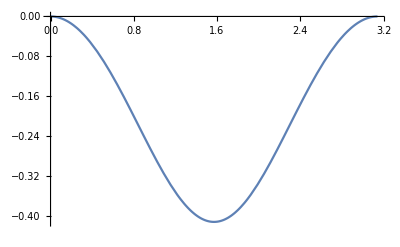

```mathematica
Plot[ω[[4]]//.{M->1,a->1/2,Q->0,r->rEH}//N,{θ,0,Pi}]
```

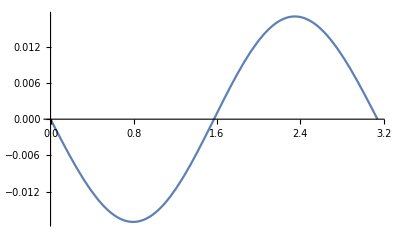

```mathematica
Plot[ω[[3]]//.{M->1,a->1/2,Q->0,r->rEH}//N,{θ,0,Pi}]
```

```mathematica
2Pi Integrate[-0.4Sin[θ]^2Sin[θ],{θ,0,Pi}]/(-8Pi)
```

0.133333